```mathematica
AppendTo[$Path, NotebookDirectory[]];
<<ColorSpacePackage`
```

```mathematica
Format[maxA,TraditionalForm]="(ϕ^⋀)_a" ;Format[minA,TraditionalForm]="(ϕ^⋁)_a";Format[maxB,TraditionalForm]="(ϕ^⋀)_b";
Format[minB,TraditionalForm]="(ϕ^⋁)_b";
Format[interX,TraditionalForm]="ϕ^x";
Format[midM,TraditionalForm]="m̄";


TraditionalForm[minB[]]
```

({m,n}↦thetaMin(m,n)⟦2⟧)()

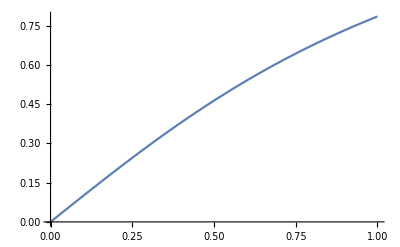

```mathematica
Plot[ArcTan[θ],{θ,0,1}]
```

The inverse function finds points out of order

```mathematica
thetaFun=Function[{y},{ArcTan[(√3 (1-y))/(3+y)],ArcTan[y/(√3)]},Listable]
```

Function[{y},{ArcTan[(√3 (1-y))/(3+y)],ArcTan[y/(√3)]},Listable]

```mathematica
Block[{n=8},
Table[
thetaFun[m 2^(3-n)],{m,0,2^(n-3)}]
]
```

{{π/6,0},{ArcTan[(31 √3)/97],ArcTan[1/(32 √3)]},{ArcTan[(15 √3)/49],ArcTan[1/(16 √3)]},{ArcTan[29/(33 √3)],ArcTan[(√3)/32]},{ArcTan[(7 √3)/25],ArcTan[1/(8 √3)]},{ArcTan[(27 √3)/101],ArcTan[5/(32 √3)]},{ArcTan[13/(17 √3)],ArcTan[(√3)/16]},{ArcTan[(25 √3)/103],ArcTan[7/(32 √3)]},{ArcTan[(3 √3)/13],ArcTan[1/(4 √3)]},{ArcTan[23/(35 √3)],ArcTan[(3 √3)/32]},{ArcTan[(11 √3)/53],ArcTan[5/(16 √3)]},{ArcTan[(21 √3)/107],ArcTan[11/(32 √3)]},{ArcTan[5/(9 √3)],ArcTan[(√3)/8]},{ArcTan[(19 √3)/109],ArcTan[13/(32 √3)]},{ArcTan[(9 √3)/55],ArcTan[7/(16 √3)]},{ArcTan[17/(37 √3)],ArcTan[(5 √3)/32]},{ArcTan[(√3)/7],ArcTan[1/(2 √3)]},{ArcTan[(15 √3)/113],ArcTan[17/(32 √3)]},{ArcTan[7/(19 √3)],ArcTan[(3 √3)/16]},{ArcTan[(13 √3)/115],ArcTan[19/(32 √3)]},{ArcTan[(3 √3)/29],ArcTan[5/(8 √3)]},{ArcTan[11/(39 √3)],ArcTan[(7 √3)/32]},{ArcTan[(5 √3)/59],ArcTan[11/(16 √3)]},{ArcTan[(9 √3)/119],ArcTan[23/(32 √3)]},{ArcTan[1/(5 √3)],ArcTan[(√3)/4]},{ArcTan[(7 √3)/121],ArcTan[25/(32 √3)]},{ArcTan[(3 √3)/61],ArcTan[13/(16 √3)]},{ArcTan[5/(41 √3)],ArcTan[(9 √3)/32]},{ArcTan[(√3)/31],ArcTan[7/(8 √3)]},{ArcTan[(3 √3)/125],ArcTan[29/(32 √3)]},{ArcTan[1/(21 √3)],ArcTan[(5 √3)/16]},{ArcTan[(√3)/127],ArcTan[31/(32 √3)]},{0,π/6}}

```mathematica
Block[{n=8},
Table[
thetaFun[(2^(n-3)-m) 2^(3-n)],{m,0,2^(n-3)}]
]
```

{{0,π/6},{ArcTan[(√3)/127],ArcTan[31/(32 √3)]},{ArcTan[1/(21 √3)],ArcTan[(5 √3)/16]},{ArcTan[(3 √3)/125],ArcTan[29/(32 √3)]},{ArcTan[(√3)/31],ArcTan[7/(8 √3)]},{ArcTan[5/(41 √3)],ArcTan[(9 √3)/32]},{ArcTan[(3 √3)/61],ArcTan[13/(16 √3)]},{ArcTan[(7 √3)/121],ArcTan[25/(32 √3)]},{ArcTan[1/(5 √3)],ArcTan[(√3)/4]},{ArcTan[(9 √3)/119],ArcTan[23/(32 √3)]},{ArcTan[(5 √3)/59],ArcTan[11/(16 √3)]},{ArcTan[11/(39 √3)],ArcTan[(7 √3)/32]},{ArcTan[(3 √3)/29],ArcTan[5/(8 √3)]},{ArcTan[(13 √3)/115],ArcTan[19/(32 √3)]},{ArcTan[7/(19 √3)],ArcTan[(3 √3)/16]},{ArcTan[(15 √3)/113],ArcTan[17/(32 √3)]},{ArcTan[(√3)/7],ArcTan[1/(2 √3)]},{ArcTan[17/(37 √3)],ArcTan[(5 √3)/32]},{ArcTan[(9 √3)/55],ArcTan[7/(16 √3)]},{ArcTan[(19 √3)/109],ArcTan[13/(32 √3)]},{ArcTan[5/(9 √3)],ArcTan[(√3)/8]},{ArcTan[(21 √3)/107],ArcTan[11/(32 √3)]},{ArcTan[(11 √3)/53],ArcTan[5/(16 √3)]},{ArcTan[23/(35 √3)],ArcTan[(3 √3)/32]},{ArcTan[(3 √3)/13],ArcTan[1/(4 √3)]},{ArcTan[(25 √3)/103],ArcTan[7/(32 √3)]},{ArcTan[13/(17 √3)],ArcTan[(√3)/16]},{ArcTan[(27 √3)/101],ArcTan[5/(32 √3)]},{ArcTan[(7 √3)/25],ArcTan[1/(8 √3)]},{ArcTan[29/(33 √3)],ArcTan[(√3)/32]},{ArcTan[(15 √3)/49],ArcTan[1/(16 √3)]},{ArcTan[(31 √3)/97],ArcTan[1/(32 √3)]},{π/6,0}}

Putting them in the reverse order

```mathematica
Simplify[thetaFun[(2^(n-3)-m) 2^(3-n)]]
```

{ArcTan[(2 √3 m)/(2^n-2 m)],ArcTan[(2^-n (2^n-8 m))/(√3)]}

```mathematica
Simplify[thetaFun[(1-y)]]
```

{ArcTan[(√3 y)/(4-y)],ArcTan[(1-y)/(√3)]}

The functions are now in the correct order

```mathematica
thetaFun=Function[{y},{ArcTan[(√3 y)/(4-y)],ArcTan[y/(√3)]},Listable];
thetaMin=Function[{m,n},Evaluate[Simplify[thetaFun[m  2^(3-n)]]]];
thetaMax=Function[{m,n},Evaluate[Simplify[thetaFun[(m +1/2) 2^(3-n)]]]];
```

```mathematica
2^(n-3)
```

2^(-3+n)

```mathematica
Grid[{{"(ϕ^⋁)_a = ",thetaMin[m,n][[1]],"  with   m = { 0,1,2,3 ... 2^(n - 3) }"  },
{"(ϕ^⋁)_b = ",thetaMin[m,n][[2]],"  with   m = { 0,1,2,3 ... 2^(n - 3) }"},
{"(ϕ^⋀)_a = ",thetaMax[m,n][[1]],"  with   m = { 0,1,2,3 ... 2^(n - 3) - 1}"},
{"(ϕ^⋀)_b = ",thetaMax[m,n][[2]],"  with   m = { 0,1,2,3 ... 2^(n - 3) - 1}"}}]
```

(ϕ^⋁)_a =  | ArcTan[(2 √3 m)/(2^n-2 m)] |   with   m = { 0,1,2,3 ... 2^(n - 3) }
(ϕ^⋁)_b =  | ArcTan[(2^(3-n) m)/(√3)] |   with   m = { 0,1,2,3 ... 2^(n - 3) }
(ϕ^⋀)_a =  | ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)] |   with   m = { 0,1,2,3 ... 2^(n - 3) - 1}
(ϕ^⋀)_b =  | ArcTan[(2^(2-n) (1+2 m))/(√3)] |   with   m = { 0,1,2,3 ... 2^(n - 3) - 1}

```mathematica
Clear[DrawAngle];
DrawAngle[pt1_,pt2_,pt3_]:={
Angle1=VectorAngle[{1,0},pt1-pt2];
Angle2=VectorAngle[pt3-pt2,{1,0}];
If[(pt1-pt2)[[2]]<0,Angle1=-Angle1];
If[(pt3-pt2)[[2]]<0,Angle2=-Angle2];
sAngle=Min[Angle1,Angle2];
eAngle=Max[Angle1,Angle2];
If[eAngle-sAngle<Pi,
Disk[pt2,0.2,{sAngle,eAngle}],
Disk[pt2,0.2,{eAngle,2Pi+sAngle}]]
};
h1=Subscript["h","1"];
h2=Subscript["h","2"];
Manipulate[
pts={{{0,1},{a,1}},{{(a-b)/2,0},{(a+b)/2,0}}};
inter=intersectionFromPoints[{pts[[1,1]],pts[[2,2]]},{pts[[2,1]],pts[[1,2]]}];
ht1=inter[[2]];
ht2=(1-inter[[2]]);
hights1={Black,Dashed,Line[{{a/2,0},inter}],Text[Style[h1,Medium,Bold],{a/2,ht1/3},{0,0},{1,0},Background->White]};
hights2={Darker[Orange],Dashed,Line[{{a/2,1},inter}],Text[Style[h2,Medium,Bold],{a/2,1-ht2/2},{0,0},{1,0},Background->White]};
base1={Darker[Orange],Dashed,Line[{{0,1},{a,1}}],Text[Style["a",Medium,Bold],{a/2,1},{0,-1},{1,0},Background->White],
Text[Style["(ϕ^⋀)_a",Medium,Bold,Black],{0,1},{0,-1},{1,0},Background->White],
Text[Style["(ϕ^⋀)_b",Medium,Bold,Black],{a,1},{0,-1},{1,0},Background->White]};
base2={Darker[Orange],Dashed,Line[{pts[[2,1]],pts[[2,2]]}],Text[Style["b",Medium,Bold],(pts[[2,1]]+pts[[2,2]])/2,{0,1},{1,0},Background->White],
Text[Style["(ϕ^⋁)_a",Medium,Bold,Black],pts[[2,1]],{0,1},{1,0},Background->White],
Text[Style["(ϕ^⋁)_b",Medium,Bold,Black],pts[[2,2]],{0,1},{1,0},Background->White]};

GraphicsRow[{Graphics[{Line[{pts[[1,1]],pts[[2,2]]}],Line[{pts[[2,1]],pts[[1,2]]}],Green,DrawAngle[pts[[1,2]],pts[[2,1]],pts[[2,2]]],DrawAngle[pts[[1,1]],pts[[2,2]],pts[[2,1]]],DrawAngle[pts[[1,2]],pts[[1,1]],pts[[2,2]]],DrawAngle[pts[[1,1]],pts[[1,2]],pts[[2,1]]],Orange,DrawAngle[pts[[1,1]],inter,pts[[1,2]]],DrawAngle[pts[[2,1]],inter,pts[[2,2]]],hights1,hights2,base1,base2},Frame->True,FrameTicks->{None,{{0,0},{1,1},{2,2}}},PlotRange->{{Min[pts[[1,1,1]],pts[[2,1,1]]]-0.2,2.2+Min[pts[[1,1,1]],pts[[2,1,1]]]},{-0.2,1.2}},AspectRatio->1 ],Grid[{{TraditionalForm[h1/h2 =="b"/"a"]},{TraditionalForm[h1 + h2==1  ]},{TraditionalForm[h1 =="b"/("a"+"b") ]}},Frame->True,Dividers->All,ItemSize->All]},Alignment->{Left,Top},BaselinePosition-> Top],
{{a,2},0,2},{{b,1},0,2}]
```

```mathematica
a=(ϕ^⋀)_b-(ϕ^⋀)_a
b=(ϕ^⋁)_b-(ϕ^⋁)_a
```

```mathematica
b=thetaMin[m,n][[2]]-thetaMin[m,n][[1]]
a=thetaMax[m,n][[2]]-thetaMax[m,n][[1]]
approxSimplify[b/(a+b)<τ]
```

ArcTan[(2^(3-n) m)/(√3)]-ArcTan[(2 √3 m)/(2^n-2 m)]

ArcTan[(2^(2-n) (1+2 m))/(√3)]-ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)]

(ArcTan[(2^(3-n) m)/(√3)]-ArcTan[(2 √3 m)/(2^n-2 m)])/(ArcTan[(2^(3-n) m)/(√3)]-ArcTan[(2 √3 m)/(2^n-2 m)]+ArcTan[(2^(2-n) (1+2 m))/(√3)]-ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)])<τ

```mathematica
Expand[TrigToExp[(ArcTan[(2^(3-n) m)/(√3)]-ArcTan[(2 √3 m)/(2^n-2 m)])/(ArcTan[(2^(3-n) m)/(√3)]-ArcTan[(2 √3 m)/(2^n-2 m)]+ArcTan[(2^(2-n) (1+2 m))/(√3)]-ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)])]]<τ
```

(ⅈ Log[1-(ⅈ 2^(3-n) m)/(√3)])/(2 (1/2 ⅈ (Log[1-(ⅈ 2^(3-n) m)/(√3)]-Log[1+(ⅈ 2^(3-n) m)/(√3)])-1/2 ⅈ (Log[1-(2 ⅈ √3 m)/(2^n-2 m)]-Log[1+(2 ⅈ √3 m)/(2^n-2 m)])+1/2 ⅈ (Log[1-(ⅈ 2^(2-n) (1+2 m))/(√3)]-Log[1+(ⅈ 2^(2-n) (1+2 m))/(√3)])-1/2 ⅈ (Log[1-(ⅈ √3 (1+2 m))/(-1+2^n-2 m)]-Log[1+(ⅈ √3 (1+2 m))/(-1+2^n-2 m)])))-(ⅈ Log[1+(ⅈ 2^(3-n) m)/(√3)])/(2 (1/2 ⅈ (Log[1-(ⅈ 2^(3-n) m)/(√3)]-Log[1+(ⅈ 2^(3-n) m)/(√3)])-1/2 ⅈ (Log[1-(2 ⅈ √3 m)/(2^n-2 m)]-Log[1+(2 ⅈ √3 m)/(2^n-2 m)])+1/2 ⅈ (Log[1-(ⅈ 2^(2-n) (1+2 m))/(√3)]-Log[1+(ⅈ 2^(2-n) (1+2 m))/(√3)])-1/2 ⅈ (Log[1-(ⅈ √3 (1+2 m))/(-1+2^n-2 m)]-Log[1+(ⅈ √3 (1+2 m))/(-1+2^n-2 m)])))-(ⅈ Log[1-(2 ⅈ √3 m)/(2^n-2 m)])/(2 (1/2 ⅈ (Log[1-(ⅈ 2^(3-n) m)/(√3)]-Log[1+(ⅈ 2^(3-n) m)/(√3)])-1/2 ⅈ (Log[1-(2 ⅈ √3 m)/(2^n-2 m)]-Log[1+(2 ⅈ √3 m)/(2^n-2 m)])+1/2 ⅈ (Log[1-(ⅈ 2^(2-n) (1+2 m))/(√3)]-Log[1+(ⅈ 2^(2-n) (1+2 m))/(√3)])-1/2 ⅈ (Log[1-(ⅈ √3 (1+2 m))/(-1+2^n-2 m)]-Log[1+(ⅈ √3 (1+2 m))/(-1+2^n-2 m)])))+(ⅈ Log[1+(2 ⅈ √3 m)/(2^n-2 m)])/(2 (1/2 ⅈ (Log[1-(ⅈ 2^(3-n) m)/(√3)]-Log[1+(ⅈ 2^(3-n) m)/(√3)])-1/2 ⅈ (Log[1-(2 ⅈ √3 m)/(2^n-2 m)]-Log[1+(2 ⅈ √3 m)/(2^n-2 m)])+1/2 ⅈ (Log[1-(ⅈ 2^(2-n) (1+2 m))/(√3)]-Log[1+(ⅈ 2^(2-n) (1+2 m))/(√3)])-1/2 ⅈ (Log[1-(ⅈ √3 (1+2 m))/(-1+2^n-2 m)]-Log[1+(ⅈ √3 (1+2 m))/(-1+2^n-2 m)])))<τ

```mathematica
b=thetaMin[m+1,n][[1]]-thetaMin[m,n][[2]]
a=thetaMax[m+1,n][[1]]-thetaMax[m,n][[2]]
approxSimplify[b/(a+b)<τ]
```

-ArcTan[(2^(3-n) m)/(√3)]+ArcTan[(2 √3 (1+m))/(2^n-2 (1+m))]

-ArcTan[(2^(2-n) (1+2 m))/(√3)]+ArcTan[(√3 (1+2 (1+m)))/(-1+2^n-2 (1+m))]

(ArcTan[(2^(3-n) m)/(√3)]-ArcTan[(2 √3 (1+m))/(-2+2^n-2 m)])/(ArcTan[(2^(3-n) m)/(√3)]-ArcTan[(2 √3 (1+m))/(-2+2^n-2 m)]+ArcTan[(2^(2-n) (1+2 m))/(√3)]-ArcTan[(√3 (3+2 m))/(-3+2^n-2 m)])<τ

```mathematica
Mod[4,4]
```

0

```mathematica
Block[{n=8},
Table[
thetaFun[m 2^(3-n)],{m,0,2^(n-3)}]
]
```

{{0,0},{ArcTan[(√3)/127],ArcTan[1/(32 √3)]},{ArcTan[1/(21 √3)],ArcTan[1/(16 √3)]},{ArcTan[(3 √3)/125],ArcTan[(√3)/32]},{ArcTan[(√3)/31],ArcTan[1/(8 √3)]},{ArcTan[5/(41 √3)],ArcTan[5/(32 √3)]},{ArcTan[(3 √3)/61],ArcTan[(√3)/16]},{ArcTan[(7 √3)/121],ArcTan[7/(32 √3)]},{ArcTan[1/(5 √3)],ArcTan[1/(4 √3)]},{ArcTan[(9 √3)/119],ArcTan[(3 √3)/32]},{ArcTan[(5 √3)/59],ArcTan[5/(16 √3)]},{ArcTan[11/(39 √3)],ArcTan[11/(32 √3)]},{ArcTan[(3 √3)/29],ArcTan[(√3)/8]},{ArcTan[(13 √3)/115],ArcTan[13/(32 √3)]},{ArcTan[7/(19 √3)],ArcTan[7/(16 √3)]},{ArcTan[(15 √3)/113],ArcTan[(5 √3)/32]},{ArcTan[(√3)/7],ArcTan[1/(2 √3)]},{ArcTan[17/(37 √3)],ArcTan[17/(32 √3)]},{ArcTan[(9 √3)/55],ArcTan[(3 √3)/16]},{ArcTan[(19 √3)/109],ArcTan[19/(32 √3)]},{ArcTan[5/(9 √3)],ArcTan[5/(8 √3)]},{ArcTan[(21 √3)/107],ArcTan[(7 √3)/32]},{ArcTan[(11 √3)/53],ArcTan[11/(16 √3)]},{ArcTan[23/(35 √3)],ArcTan[23/(32 √3)]},{ArcTan[(3 √3)/13],ArcTan[(√3)/4]},{ArcTan[(25 √3)/103],ArcTan[25/(32 √3)]},{ArcTan[13/(17 √3)],ArcTan[13/(16 √3)]},{ArcTan[(27 √3)/101],ArcTan[(9 √3)/32]},{ArcTan[(7 √3)/25],ArcTan[7/(8 √3)]},{ArcTan[29/(33 √3)],ArcTan[29/(32 √3)]},{ArcTan[(15 √3)/49],ArcTan[(5 √3)/16]},{ArcTan[(31 √3)/97],ArcTan[31/(32 √3)]},{π/6,π/6}}

```mathematica
Block[{n=8},
Table[
N[thetaFun[(m+1/2) 2^(3-n)]],{m,0,2^(n-3)-1}]
]
```

{{0.00679225,0.00902085},{0.0205353,0.0270567},{0.0344893,0.0450749},{0.0486538,0.0630639},{0.0630276,0.0810122},{0.0776094,0.0989083},{0.0923973,0.116741},{0.107389,0.1345},{0.122583,0.152173},{0.137974,0.169751},{0.15356,0.187224},{0.169338,0.204582},{0.185301,0.221816},{0.201446,0.238917},{0.217766,0.255877},{0.234257,0.272688},{0.250911,0.289342},{0.267722,0.305832},{0.284681,0.322153},{0.301782,0.338298},{0.319016,0.354261},{0.336374,0.370038},{0.353847,0.385625},{0.371426,0.401016},{0.389099,0.41621},{0.406858,0.431201},{0.424691,0.445989},{0.442587,0.460571},{0.460535,0.474945},{0.478524,0.489109},{0.496542,0.503064},{0.514578,0.516807}}

```mathematica
N[Pi/6]
```

0.523599

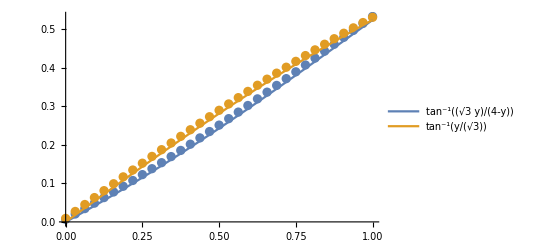

```mathematica
Block[{n=8},
pts=Table[
θ=thetaFun[(m+1/2) 2^(3-n)];{{m 2^(3-n),θ[[1]]},{m 2^(3-n),θ[[2]]}},{m,0,2^(n-3)}];
Show[{ListPlot[{pts[[All,1]],pts[[All,2]]}],Plot[Evaluate[thetaFun[y]],{y,0,1},PlotLegends->"Expressions"]}]
]
```

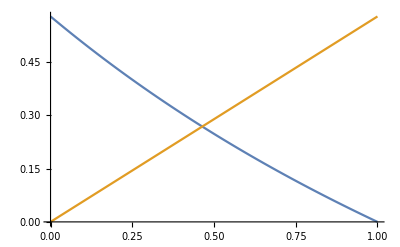

```mathematica
Plot[{(√3 (1-y))/(3+y),y/(√3)},{y,0,1}]
```

```mathematica
Solve[ArcTan[(√3 (1-y))/(3+y)]==ArcTan[y/(√3)]]
```

{{y→-3-2 √3},{y→-3+2 √3}}

```mathematica
y->-3+2 √3
```

y→-3+2 √3

```mathematica
thetaFun[m 2^(3-n)]
```

{ArcTan[(√3 (1-2^(3-n) m))/(3+2^(3-n) m)],ArcTan[(2^(3-n) m)/(√3)]}

```mathematica
thetaCrit=Function[{n},Ceiling[2^(-3+n) (-3+2 √3)]]
```

Function[{n},Ceiling[2^(-3+n) (-3+2 √3)]]

```mathematica
approxSimplify[ Reduce[(√3 (1-2^(3-n) m))/(3+2^(3-n) m)≤ (2^(3-n) m)/(√3)]]
```

m≥2^(-3+n) (-3+2 √3)

3 (1-2^(3-n) m)≤2^(3-n) m (3+2^(3-n) m)

```mathematica
N[-3+2 √3]
```

0.464102

```mathematica
m≥2^(-3+n) (-3+2 √3)
```

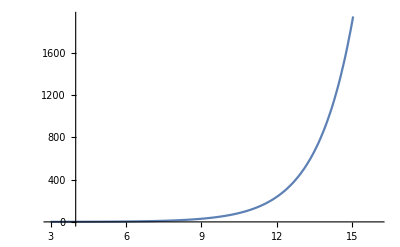

```mathematica
Plot[2^(-3+n) (-3+2 √3),{n,3,16}]
```

```mathematica
Block[{nMax=16},
Table[
c=Map[(#[[1]]<=#[[2]])&,Table[thetaFun[m 2^(3-n)],{m,0,2^(n-3)}]];
{thetaCrit[n],Count[c,False],Count[c,True]},{n,3,nMax}]
]
```

{{1,0,2},{1,0,3},{2,0,5},{4,0,9},{8,0,17},{15,0,33},{30,0,65},{60,0,129},{119,0,257},{238,0,513},{476,0,1025},{951,0,2049},{1901,0,4097},{3802,0,8193}}

```mathematica
thetaCrit[8]
```

14

#### Intersections

```mathematica
thetaMin=Function[{m,n},{ArcTan[(2 √3 m)/(2^n-2 m)],ArcTan[(2^(3-n) m)/(√3)]}];
```

```mathematica
thetaMax=Function[{m,n},{ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)],ArcTan[(2^(2-n) (1+2 m))/(√3)]}];
```

```mathematica
thetaInter=Function[{m,n},ArcTan[(-7+2^(3-n) m+√(49-2^(4-n) m+2^(6-2 n) m^2))/(2 √3)]];
```

```mathematica
fRe = Function[{θ}, (-2^(-1))*(1 + Sqrt[3]*Tan[θ])];δqRe=Function[{δθ,f,n},(Round[2^(n-2) f[δθ]]-2^(n-2) f[δθ])];
funs=Function[{δθ,f,n,fs},Evaluate[{{fs[δθ,f,n], fs[-δθ,f,n]},{ fs[π/6-δθ,f,n], fs[-(π/6-δθ),f,n]}}]];
```

```mathematica
funs[θ,fRe,n,δqRe]
```

{{Round[2^(-3+n) (-1-√3 Tan[θ])]-2^(-3+n) (-1-√3 Tan[θ]),Round[2^(-3+n) (-1+√3 Tan[θ])]-2^(-3+n) (-1+√3 Tan[θ])},{Round[2^(-3+n) (-1-√3 Tan[π/6-θ])]-2^(-3+n) (-1-√3 Tan[π/6-θ]),Round[2^(-3+n) (-1+√3 Tan[π/6-θ])]-2^(-3+n) (-1+√3 Tan[π/6-θ])}}

```mathematica
Clear[θ,n,m,δθ,funs]
```

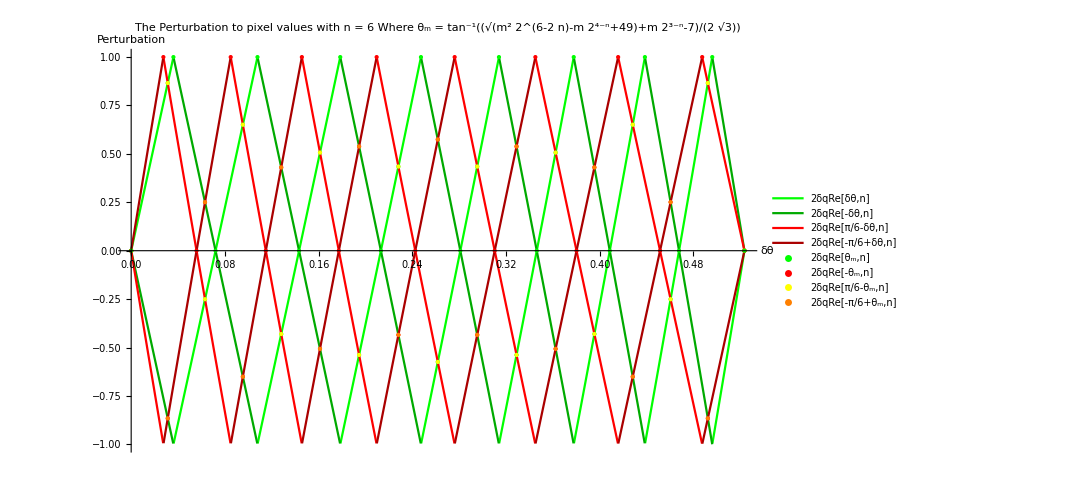

```mathematica
Block[{n=6},
thetaMinsA=Table[{thetaMin[m,n][[1]],0},{m,0,2^(n-3)}];
thetaMinsB=Table[{thetaMin[m,n][[2]],0},{m,0,2^(n-3)}];
thetaMaxsA=Table[{thetaMax[m,n][[1]],1},{m,0,2^(n-3)}];
thetaMaxsB=Table[{thetaMax[m,n][[2]],1},{m,0,2^(n-3)}];
thetaInte=Table[thetaInter[m,n],{m,0,2^(n-2)}];
ptbInter=Map[(y=2 funs[#,fRe,n,δqRe];{{{#,y[[1,1]]},{#,y[[1,2]]}},{{#,y[[2,1]]},{#,y[[2,2]]}}})&,thetaInte];
plt1=Plot[Evaluate[  2 funs[δθ,fRe,n,δqRe][[1]]],{δθ,0,Pi/6},PlotLegends->{Row[{2,"δqRe"[δθ,"n"]}],Row[{2,"δqRe"[-δθ,"n"]}]},Ticks->{PiTicks[0,Pi/2,12],All},PlotLabel->Row[{"The Perturbation to the pixel values in the second row with n = ",n}],PlotStyle->{Green,Darker[Green]},AxesLabel->{"δθ","Perturbation"}];
plt2=Plot[Evaluate[  2 funs[δθ,fRe,n,δqRe][[2]]],{δθ,0,Pi/6},PlotLegends->{Row[{2,"δqRe"[π/6-δθ,"n"]}],Row[{2,"δqRe"[-(π/6-δθ),"n"]}]},Ticks->{PiTicks[0,Pi/2,12],All},PlotLabel->Row[{"The Perturbation to the pixel values in the third row with n = ",n}],PlotStyle->{Red,Darker[Red]}];
plt3=ListPlot[{ptbInter[[All,1,1]],ptbInter[[All,1,2]],ptbInter[[All,2,1]],ptbInter[[All,2,2]],thetaMinsA,thetaMinsB,thetaMaxsA,thetaMaxsB},PlotStyle->{Directive[Green,PointSize[Large]],Directive[Red,PointSize[Large]],Directive[Yellow,PointSize[Medium]],Directive[Orange,PointSize[Medium]],Directive[Red,PointSize[Large]],Directive[Green,PointSize[Large]],Directive[Red,PointSize[Large]],Directive[Green,PointSize[Large]]},PlotLegends->{Row[{2,"δqRe"[Subscript[θ, m],"n"]}],Row[{2,"δqRe"[-Subscript[θ, m],"n"]}],Row[{2,"δqRe"[π/6-Subscript[θ, m],"n"]}],Row[{2,"δqRe"[-(π/6-Subscript[θ, m]),"n"]}]}];
Show[{plt1,plt2,plt3},PlotLabel->Column[{Row[{"The Perturbation to pixel values with n = ",n}],Row[{"Where " ,"θ_m = ", TraditionalForm[ArcTan[(-7+2^(3-"n") m+Sqrt[49-2^(4-"n") m+2^(6-2 "n") m^2])/(2 Sqrt[3])]]}]}],ImageSize->800]
]
```

```mathematica
Block[{n=8},Table[N[thetaMin[m,n]],{m,0,2^(n-3)}]]
```

{{0.,0.},{0.0136373,0.0180402},{0.0274859,0.0360687},{0.0415453,0.0540738},{0.0558146,0.0720439},{0.0702926,0.0899675},{0.0849777,0.107833},{0.0998679,0.12563},{0.114961,0.143348},{0.130254,0.160975},{0.145743,0.178502},{0.161425,0.195918},{0.177296,0.213216},{0.193351,0.230384},{0.209584,0.247416},{0.225991,0.264302},{0.242564,0.281035},{0.259297,0.297608},{0.276183,0.314014},{0.293215,0.330248},{0.310383,0.346302},{0.32768,0.362173},{0.345097,0.377856},{0.362624,0.393345},{0.380251,0.408638},{0.397969,0.423731},{0.415766,0.438621},{0.433631,0.453306},{0.451555,0.467784},{0.469525,0.482053},{0.48753,0.496113},{0.505559,0.509961},{0.523599,0.523599}}

```mathematica
Format[maxA,TraditionalForm]="(ϕ^⋀)_a" ;Format[minA,TraditionalForm]="(ϕ^⋁)_a";Format[maxB,TraditionalForm]="(ϕ^⋀)_b";
Format[minB,TraditionalForm]="(ϕ^⋁)_b";
Format[interX,TraditionalForm]="ϕ^x";
TraditionalForm[minB]
```

tan^-1(m/(32 √3))

```mathematica
minA=Function[{m,n},thetaMin[m,n][[1]]];
minB=Function[{m,n},thetaMin[m,n][[2]]];
maxA=Function[{m,n},thetaMax[m,n][[1]]];
maxB=Function[{m,n},thetaMax[m,n][[2]]];
```

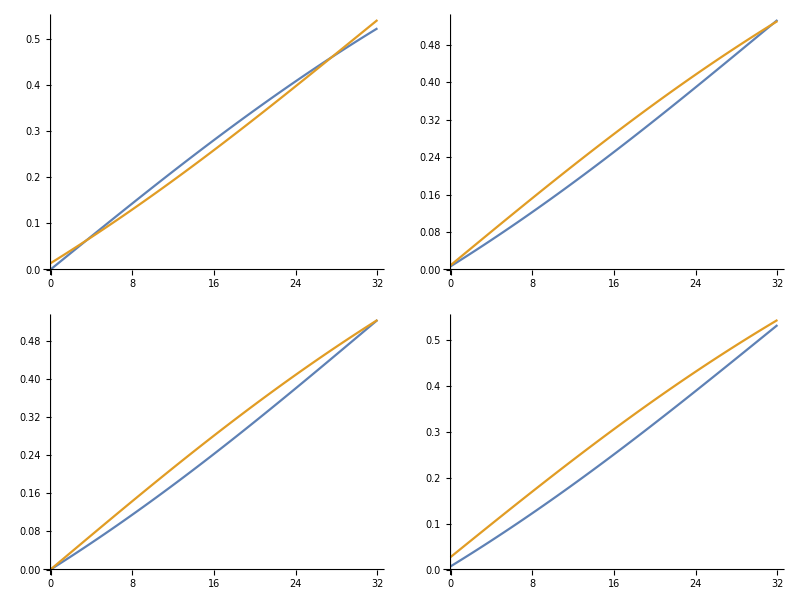

```mathematica
Block[{n=8},
minA=Function[{m},thetaMin[m,n][[1]]];
minB=Function[{m},thetaMin[m,n][[2]]];
maxA=Function[{m},thetaMax[m,n][[1]]];
maxB=Function[{m},thetaMax[m,n][[2]]];
Grid[{{Plot[{minB[m],minA[m+1]},{m,0,2^(n-3)}],
Plot[{maxA[m],maxB[m]},{m,0,2^(n-3)}]},{
Plot[{minA[m],minB[m]},{m,0,2^(n-3)}],
Plot[{maxA[m],maxB[m+1]},{m,0,2^(n-3)}]}}]
]
```

```mathematica
minAf=Function[{m,n},thetaMin[m,n][[1,1]]];
minBf=Function[{m,n},thetaMin[m,n][[2,1]]];
maxAf=Function[{m,n},thetaMax[m,n][[1,1]]];
maxBf=Function[{m,n},thetaMax[m,n][[2,1]]];
{minBf[m,n]==minAf[m+1,n],maxAf[m,n]==maxBf[m,n],minAf[m,n]==minBf[m,n],maxAf[m,n]==maxBf[m+1,n]}
Map[approxSimplify[Reduce[#]]&,%]
```

{(2^(3-n) m)/(√3)==(2 √3 (1+m))/(2^n-2 (1+m)),(√3 (1+2 m))/(-1+2^n-2 m)==(2^(2-n) (1+2 m))/(√3),(2 √3 m)/(2^n-2 m)==(2^(3-n) m)/(√3),(√3 (1+2 m))/(-1+2^n-2 m)==(2^(2-n) (1+2 (1+m)))/(√3)}

{(8 m (1+m))/(-3+m)==2^n,2^n==4+8 m,2^n==8 m,2^n (9+2 m)==4 (3+4 m (2+m))}

```mathematica
ThetaFlip[8]
Flip[2,8]
ThetaCond[m,8]
```

{{31/2-(√577)/2,31/2+(√577)/2},{15-(√577)/2,15+(√577)/2}}

{False,False}

{31/2-(√577)/2≤m≤31/2+(√577)/2,15-(√577)/2≤m≤15+(√577)/2}

```mathematica
oddBounds[m_,n_]={{maxA[m,n],maxB[m,n]},{minB[m,n],minA[m+1,n]}};
evenBounds[m_,n_]={{maxB[m-1,n],maxA[m,n]},{minA[m,n],minB[m,n]}};
```

```mathematica
oddBounds[2m,n]
evenBounds[2m+1,n]
oddAoB=Function[{m,n},Evaluate[(oddBounds[m,n][[1,2]]-oddBounds[m,n][[1,1]])/(oddBounds[m,n][[2,2]]-oddBounds[m,n][[2,1]])]];
evenAoB=Function[{m,n},Evaluate[(evenBounds[m,n][[1,2]]-evenBounds[m,n][[1,1]])/(evenBounds[m,n][[2,2]]-evenBounds[m,n][[2,1]])]];
approxSimplify[oddAoB[2m,n]]
approxSimplify[evenAoB[2m+1,n]]
```

{{ArcTan[(√3 (1+4 m))/(-1+2^n-4 m)],ArcTan[(2^(2-n) (1+4 m))/(√3)]},{ArcTan[(2^(4-n) m)/(√3)],ArcTan[(2 √3 (1+2 m))/(2^n-2 (1+2 m))]}}

{{ArcTan[(2^(2-n) (1+4 m))/(√3)],ArcTan[(√3 (1+2 (1+2 m)))/(-1+2^n-2 (1+2 m))]},{ArcTan[(2 √3 (1+2 m))/(2^n-2 (1+2 m))],ArcTan[(2^(3-n) (1+2 m))/(√3)]}}

(-ArcTan[(2^(2-n) (1+4 m))/(√3)]+ArcTan[(√3 (1+4 m))/(-1+2^n-4 m)])/(ArcTan[(2^(4-n) m)/(√3)]+ArcTan[(2 √3 (1+2 m))/(2-2^n+4 m)])

(-ArcTan[(2^(2-n) (1+4 m))/(√3)]+ArcTan[(√3 (3+4 m))/(-3+2^n-4 m)])/(ArcTan[(2^(3-n) (1+2 m))/(√3)]+ArcTan[(2 √3 (1+2 m))/(2-2^n+4 m)])

```mathematica
N[oddAoB[2*15,8]]
N[evenAoB[2*15+1,8]]
```

0.690411

2.61519

```mathematica
midM[n]
```

midM[n]

```mathematica
lns
```

{Line[{{1/2 (-1+2^(-3+n))-1/2 √(1+2^(2 (-3+n))-7 2^(-2+n)),-2},{1/2 (-1+2^(-3+n))-1/2 √(1+2^(2 (-3+n))-7 2^(-2+n)),2}}],Line[{{1/2 (-1+2^(-3+n))+1/2 √(1+2^(2 (-3+n))-7 2^(-2+n)),-2},{1/2 (-1+2^(-3+n))+1/2 √(1+2^(2 (-3+n))-7 2^(-2+n)),2}}]}

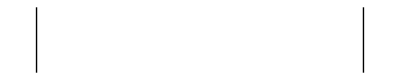

```mathematica
Graphics[lns]
```

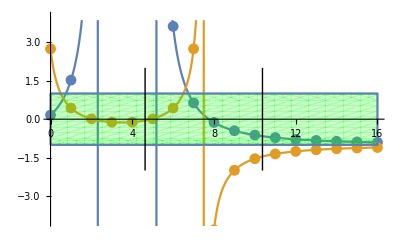

```mathematica
Block[{n=7},
oddAB=Table[
{m,oddAoB[2m,n]}
,{m,0,2^(n-3)}];
evenAB=Table[
{m,evenAoB[2m+1,n]}
,{m,0,2^(n-3)}];
lineVals={midM[n]-thetaFlipE[n],midM[n]+thetaFlipE[n]};
lns=Map[Line[{{#,-2},{#,2}}]&,lineVals];
lPlt=ListPlot[{oddAB,evenAB},PlotRange->{{0,2^(n-3)},{-4,4}}];
rPlt=RegionPlot[y≤1&&y≥ -1,{m,0,2^(n-3)},{y,-2,2},PlotStyle->Directive[Green,Opacity[0.2]]];
plt=Plot[{oddAoB[2m,n],evenAoB[2m+1,n]},{m,0,2^(n-3)},Epilog->lns];
Show[{lPlt,plt,rPlt},Epilog->lns]
]
```

```mathematica
Clear[n]
Reduce[oddAoB[2m,n]==evenAoB[2m+1,n],m]
```

Reduce[(ArcTan[(2^(2-n) (1+4 m))/(√3)]-ArcTan[(√3 (1+4 m))/(-1+2^n-4 m)])/(-ArcTan[(2^(4-n) m)/(√3)]+ArcTan[(2 √3 (1+2 m))/(2^n-2 (1+2 m))])==(-ArcTan[(2^(2-n) (1+4 m))/(√3)]+ArcTan[(√3 (1+2 (1+2 m)))/(-1+2^n-2 (1+2 m))])/(ArcTan[(2^(3-n) (1+2 m))/(√3)]-ArcTan[(2 √3 (1+2 m))/(2^n-2 (1+2 m))]),m]

```mathematica
Block[{n=8},
Table[MatrixForm[{
Flip[m,n],
ThetaCond[m,n],
{minBf[m,n]>minAf[m+1,n],maxBf[m,n]>maxAf[m+1,n]},
{minBf[m,n]-minAf[m+1,n],maxBf[m,n]-maxAf[m+1,n]},
{(minBf[m,n]-minAf[m+1,n])/(maxBf[m,n]-maxAf[m+1,n])}
}],{m,0,2^(n-3)}]]
```

{({False,False}
{False,False}
{{0,0}⟦2,1⟧>(√3)/127,False}
{-(√3)/127+{0,0}⟦2,1⟧,1/(64 √3)-(3 √3)/253}
{(-(√3)/127+{0,0}⟦2,1⟧)/(1/(64 √3)-(3 √3)/253)}),({False,False}
{False,False}
{False,False}
{-11/(672 √3),-(69 √3)/16064}
{5522/4347}),({False,False}
{False,False}
{False,False}
{1/(16 √3)-(3 √3)/125,-(11 √3)/5312}
{-(5312 (1/(16 √3)-(3 √3)/125))/(11 √3)}),({False,True}
{False,True}
{False,True}
{-(√3)/992,7/(64 √3)-(9 √3)/247}
{-(√3)/(992 (7/(64 √3)-(9 √3)/247))}),({True,True}
{True,True}
{True,True}
{1/(328 √3),(31 √3)/15680}
{1960/3813}),({True,True}
{True,True}
{True,True}
{5/(32 √3)-(3 √3)/61,59/(5184 √3)}
{5184/59 √3 (5/(32 √3)-(3 √3)/61)}),({True,True}
{True,True}
{True,True}
{(9 √3)/1936,13/(64 √3)-(15 √3)/241}
{(9 √3)/(1936 (13/(64 √3)-(15 √3)/241))}),({True,True}
{True,True}
{True,True}
{(√3)/160,(107 √3)/15296}
{478/535}),({True,True}
{True,True}
{True,True}
{1/(4 √3)-(9 √3)/119,127/(5056 √3)}
{5056/127 √3 (1/(4 √3)-(9 √3)/119)}),({True,True}
{True,True}
{True,True}
{(17 √3)/1888,19/(64 √3)-(21 √3)/235}
{(17 √3)/(1888 (19/(64 √3)-(21 √3)/235))}),({True,True}
{True,True}
{True,True}
{19/(624 √3),(159 √3)/14912}
{17708/18603}),({True,True}
{True,True}
{True,True}
{11/(32 √3)-(3 √3)/29,(57 √3)/4928}
{(4928 (11/(32 √3)-(3 √3)/29))/(57 √3)}),({True,True}
{True,True}
{True,True}
{(11 √3)/920,25/(64 √3)-(27 √3)/229}
{(11 √3)/(920 (25/(64 √3)-(27 √3)/229))}),({True,True}
{True,True}
{True,True}
{23/(608 √3),(187 √3)/14528}
{10442/10659}),({True,True}
{True,True}
{True,True}
{7/(16 √3)-(15 √3)/113,191/(4800 √3)}
{4800/191 √3 (7/(16 √3)-(15 √3)/113)}),({True,True}
{True,True}
{True,True}
{(3 √3)/224,31/(64 √3)-(33 √3)/223}
{(3 √3)/(224 (31/(64 √3)-(33 √3)/223))}),({True,True}
{True,True}
{True,True}
{(√3)/74,(191 √3)/14144}
{7072/7067}),({True,True}
{True,True}
{True,True}
{17/(32 √3)-(9 √3)/55,187/(4672 √3)}
{4672/187 √3 (17/(32 √3)-(9 √3)/55)}),({True,True}
{True,True}
{True,True}
{(23 √3)/1744,37/(64 √3)-(39 √3)/217}
{(23 √3)/(1744 (37/(64 √3)-(39 √3)/217))}),({True,True}
{True,True}
{True,True}
{11/(288 √3),(171 √3)/13760}
{4730/4617}),({True,True}
{True,True}
{True,True}
{5/(8 √3)-(21 √3)/107,(53 √3)/4544}
{(4544 (5/(8 √3)-(21 √3)/107))/(53 √3)}),({True,True}
{True,True}
{True,True}
{(19 √3)/1696,43/(64 √3)-(45 √3)/211}
{(19 √3)/(1696 (43/(64 √3)-(45 √3)/211))}),({True,True}
{True,True}
{True,True}
{17/(560 √3),(127 √3)/13376}
{14212/13335}),({True,True}
{True,True}
{True,True}
{23/(32 √3)-(3 √3)/13,107/(4416 √3)}
{4416/107 √3 (23/(32 √3)-(3 √3)/13)}),({True,True}
{True,True}
{True,True}
{(3 √3)/412,49/(64 √3)-(51 √3)/205}
{(3 √3)/(412 (49/(64 √3)-(51 √3)/205))}),({True,True}
{True,True}
{True,True}
{(3 √3)/544,(59 √3)/12992}
{1218/1003}),({True,True}
{True,True}
{True,True}
{13/(16 √3)-(27 √3)/101,31/(4288 √3)}
{4288/31 √3 (13/(16 √3)-(27 √3)/101)}),({True,True}
{True,True}
{True,True}
{(√3)/800,55/(64 √3)-(57 √3)/199}
{(√3)/(800 (55/(64 √3)-(57 √3)/199))}),({False,False}
{False,False}
{False,False}
{-1/(264 √3),-(33 √3)/12608}
{1576/3267}),({False,False}
{False,False}
{False,False}
{29/(32 √3)-(15 √3)/49,-(23 √3)/4160}
{-(4160 (29/(32 √3)-(15 √3)/49))/(23 √3)}),({False,False}
{False,False}
{False,False}
{-(11 √3)/1552,61/(64 √3)-(63 √3)/193}
{-(11 √3)/(1552 (61/(64 √3)-(63 √3)/193))}),({False,False}
{False,False}
{True,False}
{-1/6+31/(32 √3),-(149 √3)/12224}
{-(12224 (-1/6+31/(32 √3)))/(149 √3)}),({False,False}
{False,False}
{False,False}
{1/6-(33 √3)/95,-193/(4032 √3)}
{-4032/193 √3 (1/6-(33 √3)/95)})}

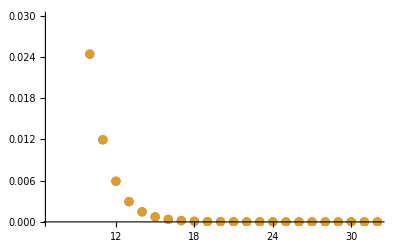

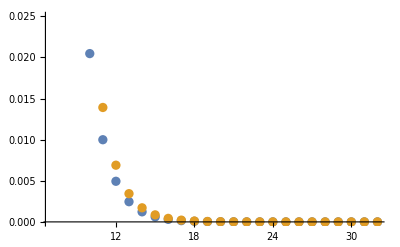

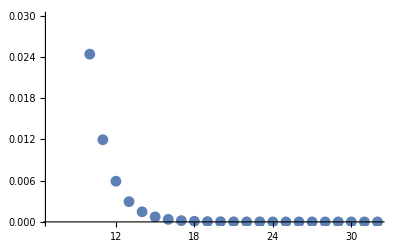

```mathematica
flip=Table[f=ThetaFlip[n];{{{n,f[[1,1]]/(2^(n-3)-1)},{n,1-f[[1,2]]/(2^(n-3)-1)}},{{n,f[[2,1]]/(2^(n-3)-1)},{n,1-f[[2,2]]/(2^(n-3)-1)}}},{n,4,32}];
ListPlot[Evaluate[{flip[[All,1,1]],flip[[All,1,2]]}]]
ListPlot[Evaluate[{flip[[All,2,1]],flip[[All,2,2]]}]]
ListPlot[flip[[All,1,2]]]
```

```mathematica
ThetaFlip=Function[{n},Evaluate[m/.Map[Solve[#,m]&,{(8 m (1+m))/(-3+m)==2^n,2^n==4+8 m,2^n==8 m,2^n (9+2 m)==4 (3+4 m (2+m))}]]]
```

Function[{n},{{1/16 (-8+2^n-√(64+2^(2 n)-7 2^(4+n))),1/16 (-8+2^n+√(64+2^(2 n)-7 2^(4+n)))},{1/8 (-4+2^n)},{2^(-3+n)},{1/32 (-32+2^(1+n)-2 √(64+2^(2 n)+7 2^(4+n))),1/32 (-32+2^(1+n)+2 √(64+2^(2 n)+7 2^(4+n)))}}]

```mathematica
approxSimplify
```

Function[{expr},Assuming[m∈Integers&&m>0&&m≤n&&n∈Integers&&n>3&&θ∈Reals&&θ≥0&&θ<π&&δθ∈Reals&&δθ≥0&&δθ<π/6,FullSimplify[expr]]]

```mathematica
approxSimplify[ThetaFlip[n]]
```

{{1/16 (-8+2^n-√(64-7 2^(4+n)+4^n)),1/16 (-8+2^n+√(64-7 2^(4+n)+4^n))},{1/8 (-4+2^n)},{2^(-3+n)},{1/16 (-16+2^n-√(64+7 2^(4+n)+4^n)),1/16 (-16+2^n+√(64+7 2^(4+n)+4^n))}}

```mathematica
N[ThetaFlip[8]]
```

{{3.48959,27.5104},{31.5},{32.},{-4.18984,34.1898}}

```mathematica
approxSimplify[Reduce[(2^(3-n) m)/(√3)==(2 √3 (1+m))/(2^n-2 (1+m))]]
Solve[%,m]
```

(8 m (1+m))/(-3+m)==2^n

{{m→1/16 (-8+2^n-√(64+2^(2 n)-7 2^(4+n)))},{m→1/16 (-8+2^n+√(64+2^(2 n)-7 2^(4+n)))}}

```mathematica
N[1/16 (-8+2^n+√(64+2^(2 n)-7 2^(4+n)))]/.n->8
```

27.5104

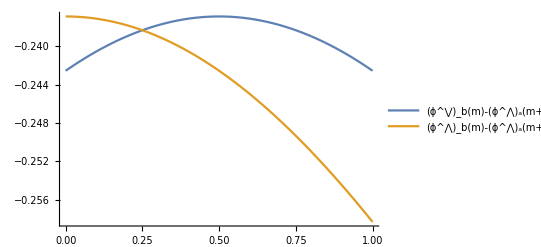
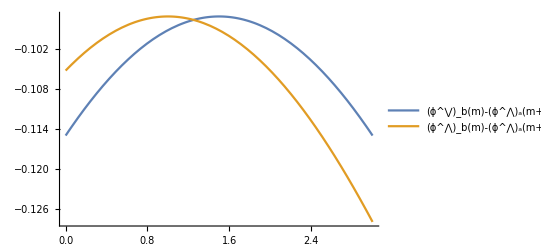
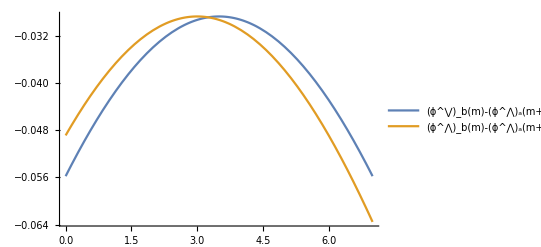
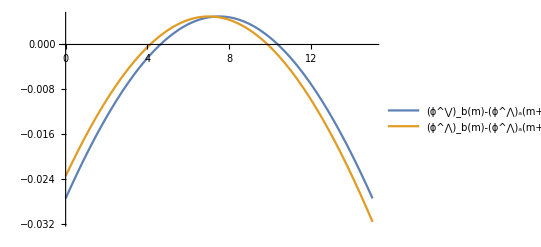
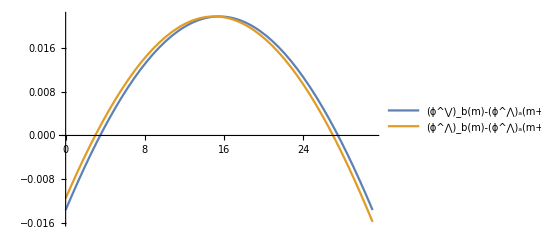
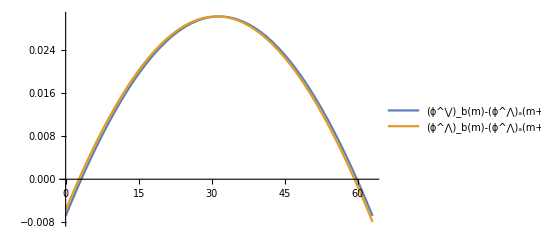
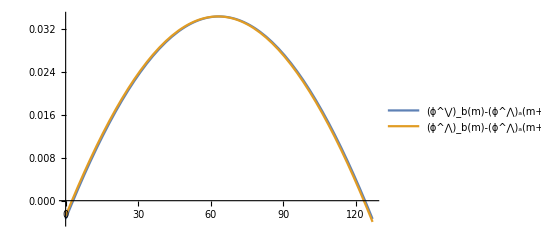
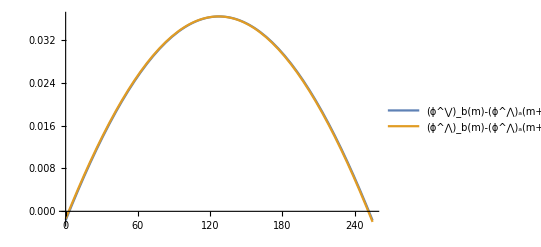

```mathematica
Block[{n=8},
Table[
minA=Function[{m},thetaMin[m,n][[1]]];
minB=Function[{m},thetaMin[m,n][[2]]];
maxA=Function[{m},thetaMax[m,n][[1]]];
maxB=Function[{m},thetaMax[m,n][[2]]];
Plot[{minB[m]-minA[m+1],maxB[m]-maxA[m+1]},{m,0,2^(n-3)-1},PlotLegends->"Expressions"],
{n,4,32}]
]
```

```mathematica
Block[{n=8},
minA=Function[{m},thetaMin[m,n][[1]]];
minB=Function[{m},thetaMin[m,n][[2]]];
maxA=Function[{m},thetaMax[m,n][[1]]];
maxB=Function[{m},thetaMax[m,n][[2]]];
Table[
Column[{
Row[{"(ϕ^⋁)_b"[m]≤ "ϕ^x"[2 m+1,n]≤"(ϕ^⋁)_a"[m+1],"  =  ",minB[m]≤ thetaInter[2 m+1,n]≤ minA[m+1],"  =  ",N@minB[m],"≤", N@thetaInter[2 m+1,n],"≤", N@minA[m+1]}],
Row[{"(ϕ^⋀)_a"[m]≤ "ϕ^x"[2 m+1,n]≤"(ϕ^⋀)_b"[m],"  =  ",maxA[m]≤ thetaInter[2 m+1,n]≤ maxB[m],"  =  ",N@maxA[m],"≤",N@ thetaInter[2 m+1,n],"≤", N@maxB[m]}],
Row[{"(ϕ^⋁)_a"[m]≤ "ϕ^x"[2 m,n]≤" (ϕ^⋁)_b"[m],"  =  ",minA[m]≤ thetaInter[2 m,n]≤ minB[m],"  =  ",N@minA[m],"≤",N@ thetaInter[2 m,n],"≤", N@minB[m]}],
Row[{"(ϕ^⋀)_b"[m-2]≤ "ϕ^x"[2 m,n]≤" (ϕ^⋀)_a"[m-1],"  =  ",maxA[m-2]≤ thetaInter[2 m,n]≤ maxB[m-1],"  =  ",N@maxA[m-2],"≤",N@ thetaInter[2 m,n],"≤", N@maxB[m-1]}]}],
{m,0,2^(n-3)}]
]
```

{(ϕ^⋁)_b[0]≤ϕ^x[1,8]≤(ϕ^⋁)_a[1]  =  True  =  0.≤0.00775195≤0.0136373
(ϕ^⋀)_a[0]≤ϕ^x[1,8]≤(ϕ^⋀)_b[0]  =  True  =  0.00679225≤0.00775195≤0.00902085
(ϕ^⋁)_a[0]≤ϕ^x[0,8]≤ (ϕ^⋁)_b[0]  =  True  =  0.≤0.≤0.
(ϕ^⋀)_b[-2]≤ϕ^x[0,8]≤ (ϕ^⋀)_a[-1]  =  False  =  -0.0200597≤0.≤-0.00902085,(ϕ^⋁)_b[1]≤ϕ^x[3,8]≤(ϕ^⋁)_a[2]  =  True  =  0.0180402≤0.0233707≤0.0274859
(ϕ^⋀)_a[1]≤ϕ^x[3,8]≤(ϕ^⋀)_b[1]  =  True  =  0.0205353≤0.0233707≤0.0270567
(ϕ^⋁)_a[1]≤ϕ^x[2,8]≤ (ϕ^⋁)_b[1]  =  True  =  0.0136373≤0.0155425≤0.0180402
(ϕ^⋀)_b[-1]≤ϕ^x[2,8]≤ (ϕ^⋀)_a[0]  =  False  =  -0.0067394≤0.0155425≤0.00902085,(ϕ^⋁)_b[2]≤ϕ^x[5,8]≤(ϕ^⋁)_a[3]  =  True  =  0.0360687≤0.0391365≤0.0415453
(ϕ^⋀)_a[2]≤ϕ^x[5,8]≤(ϕ^⋀)_b[2]  =  True  =  0.0344893≤0.0391365≤0.0450749
(ϕ^⋁)_a[2]≤ϕ^x[4,8]≤ (ϕ^⋁)_b[2]  =  True  =  0.0274859≤0.0312357≤0.0360687
(ϕ^⋀)_b[0]≤ϕ^x[4,8]≤ (ϕ^⋀)_a[1]  =  False  =  0.00679225≤0.0312357≤0.0270567,(ϕ^⋁)_b[3]≤ϕ^x[7,8]≤(ϕ^⋁)_a[4]  =  True  =  0.0540738≤0.0550416≤0.0558146
(ϕ^⋀)_a[3]≤ϕ^x[7,8]≤(ϕ^⋀)_b[3]  =  True  =  0.0486538≤0.0550416≤0.0630639
(ϕ^⋁)_a[3]≤ϕ^x[6,8]≤ (ϕ^⋁)_b[3]  =  True  =  0.0415453≤0.0470721≤0.0540738
(ϕ^⋀)_b[1]≤ϕ^x[6,8]≤ (ϕ^⋀)_a[2]  =  False  =  0.0205353≤0.0470721≤0.0450749,(ϕ^⋁)_b[4]≤ϕ^x[9,8]≤(ϕ^⋁)_a[5]  =  False  =  0.0720439≤0.0710777≤0.0702926
(ϕ^⋀)_a[4]≤ϕ^x[9,8]≤(ϕ^⋀)_b[4]  =  True  =  0.0630276≤0.0710777≤0.0810122
(ϕ^⋁)_a[4]≤ϕ^x[8,8]≤ (ϕ^⋁)_b[4]  =  True  =  0.0558146≤0.0630438≤0.0720439
(ϕ^⋀)_b[2]≤ϕ^x[8,8]≤ (ϕ^⋀)_a[3]  =  True  =  0.0344893≤0.0630438≤0.0630639,(ϕ^⋁)_b[5]≤ϕ^x[11,8]≤(ϕ^⋁)_a[6]  =  False  =  0.0899675≤0.0872363≤0.0849777
(ϕ^⋀)_a[5]≤ϕ^x[11,8]≤(ϕ^⋀)_b[5]  =  True  =  0.0776094≤0.0872363≤0.0989083
(ϕ^⋁)_a[5]≤ϕ^x[10,8]≤ (ϕ^⋁)_b[5]  =  True  =  0.0702926≤0.0791423≤0.0899675
(ϕ^⋀)_b[3]≤ϕ^x[10,8]≤ (ϕ^⋀)_a[4]  =  True  =  0.0486538≤0.0791423≤0.0810122,(ϕ^⋁)_b[6]≤ϕ^x[13,8]≤(ϕ^⋁)_a[7]  =  False  =  0.107833≤0.103508≤0.0998679
(ϕ^⋀)_a[6]≤ϕ^x[13,8]≤(ϕ^⋀)_b[6]  =  True  =  0.0923973≤0.103508≤0.116741
(ϕ^⋁)_a[6]≤ϕ^x[12,8]≤ (ϕ^⋁)_b[6]  =  True  =  0.0849777≤0.0953587≤0.107833
(ϕ^⋀)_b[4]≤ϕ^x[12,8]≤ (ϕ^⋀)_a[5]  =  True  =  0.0630276≤0.0953587≤0.0989083,(ϕ^⋁)_b[7]≤ϕ^x[15,8]≤(ϕ^⋁)_a[8]  =  False  =  0.12563≤0.119884≤0.114961
(ϕ^⋀)_a[7]≤ϕ^x[15,8]≤(ϕ^⋀)_b[7]  =  True  =  0.107389≤0.119884≤0.1345
(ϕ^⋁)_a[7]≤ϕ^x[14,8]≤ (ϕ^⋁)_b[7]  =  True  =  0.0998679≤0.111684≤0.12563
(ϕ^⋀)_b[5]≤ϕ^x[14,8]≤ (ϕ^⋀)_a[6]  =  True  =  0.0776094≤0.111684≤0.116741,(ϕ^⋁)_b[8]≤ϕ^x[17,8]≤(ϕ^⋁)_a[9]  =  False  =  0.143348≤0.136354≤0.130254
(ϕ^⋀)_a[8]≤ϕ^x[17,8]≤(ϕ^⋀)_b[8]  =  True  =  0.122583≤0.136354≤0.152173
(ϕ^⋁)_a[8]≤ϕ^x[16,8]≤ (ϕ^⋁)_b[8]  =  True  =  0.114961≤0.128108≤0.143348
(ϕ^⋀)_b[6]≤ϕ^x[16,8]≤ (ϕ^⋀)_a[7]  =  True  =  0.0923973≤0.128108≤0.1345,(ϕ^⋁)_b[9]≤ϕ^x[19,8]≤(ϕ^⋁)_a[10]  =  False  =  0.160975≤0.152907≤0.145743
(ϕ^⋀)_a[9]≤ϕ^x[19,8]≤(ϕ^⋀)_b[9]  =  True  =  0.137974≤0.152907≤0.169751
(ϕ^⋁)_a[9]≤ϕ^x[18,8]≤ (ϕ^⋁)_b[9]  =  True  =  0.130254≤0.144621≤0.160975
(ϕ^⋀)_b[7]≤ϕ^x[18,8]≤ (ϕ^⋀)_a[8]  =  True  =  0.107389≤0.144621≤0.152173,(ϕ^⋁)_b[10]≤ϕ^x[21,8]≤(ϕ^⋁)_a[11]  =  False  =  0.178502≤0.169534≤0.161425
(ϕ^⋀)_a[10]≤ϕ^x[21,8]≤(ϕ^⋀)_b[10]  =  True  =  0.15356≤0.169534≤0.187224
(ϕ^⋁)_a[10]≤ϕ^x[20,8]≤ (ϕ^⋁)_b[10]  =  True  =  0.145743≤0.161212≤0.178502
(ϕ^⋀)_b[8]≤ϕ^x[20,8]≤ (ϕ^⋀)_a[9]  =  True  =  0.122583≤0.161212≤0.169751,(ϕ^⋁)_b[11]≤ϕ^x[23,8]≤(ϕ^⋁)_a[12]  =  False  =  0.195918≤0.186224≤0.177296
(ϕ^⋀)_a[11]≤ϕ^x[23,8]≤(ϕ^⋀)_b[11]  =  True  =  0.169338≤0.186224≤0.204582
(ϕ^⋁)_a[11]≤ϕ^x[22,8]≤ (ϕ^⋁)_b[11]  =  True  =  0.161425≤0.177872≤0.195918
(ϕ^⋀)_b[9]≤ϕ^x[22,8]≤ (ϕ^⋀)_a[10]  =  True  =  0.137974≤0.177872≤0.187224,(ϕ^⋁)_b[12]≤ϕ^x[25,8]≤(ϕ^⋁)_a[13]  =  False  =  0.213216≤0.202964≤0.193351
(ϕ^⋀)_a[12]≤ϕ^x[25,8]≤(ϕ^⋀)_b[12]  =  True  =  0.185301≤0.202964≤0.221816
(ϕ^⋁)_a[12]≤ϕ^x[24,8]≤ (ϕ^⋁)_b[12]  =  True  =  0.177296≤0.194588≤0.213216
(ϕ^⋀)_b[10]≤ϕ^x[24,8]≤ (ϕ^⋀)_a[11]  =  True  =  0.15356≤0.194588≤0.204582,(ϕ^⋁)_b[13]≤ϕ^x[27,8]≤(ϕ^⋁)_a[14]  =  False  =  0.230384≤0.219746≤0.209584
(ϕ^⋀)_a[13]≤ϕ^x[27,8]≤(ϕ^⋀)_b[13]  =  True  =  0.201446≤0.219746≤0.238917
(ϕ^⋁)_a[13]≤ϕ^x[26,8]≤ (ϕ^⋁)_b[13]  =  True  =  0.193351≤0.211351≤0.230384
(ϕ^⋀)_b[11]≤ϕ^x[26,8]≤ (ϕ^⋀)_a[12]  =  True  =  0.169338≤0.211351≤0.221816,(ϕ^⋁)_b[14]≤ϕ^x[29,8]≤(ϕ^⋁)_a[15]  =  False  =  0.247416≤0.236556≤0.225991
(ϕ^⋀)_a[14]≤ϕ^x[29,8]≤(ϕ^⋀)_b[14]  =  True  =  0.217766≤0.236556≤0.255877
(ϕ^⋁)_a[14]≤ϕ^x[28,8]≤ (ϕ^⋁)_b[14]  =  True  =  0.209584≤0.228148≤0.247416
(ϕ^⋀)_b[12]≤ϕ^x[28,8]≤ (ϕ^⋀)_a[13]  =  True  =  0.185301≤0.228148≤0.238917,(ϕ^⋁)_b[15]≤ϕ^x[31,8]≤(ϕ^⋁)_a[16]  =  False  =  0.264302≤0.253383≤0.242564
(ϕ^⋀)_a[15]≤ϕ^x[31,8]≤(ϕ^⋀)_b[15]  =  True  =  0.234257≤0.253383≤0.272688
(ϕ^⋁)_a[15]≤ϕ^x[30,8]≤ (ϕ^⋁)_b[15]  =  True  =  0.225991≤0.244968≤0.264302
(ϕ^⋀)_b[13]≤ϕ^x[30,8]≤ (ϕ^⋀)_a[14]  =  True  =  0.201446≤0.244968≤0.255877,(ϕ^⋁)_b[16]≤ϕ^x[33,8]≤(ϕ^⋁)_a[17]  =  False  =  0.281035≤0.270216≤0.259297
(ϕ^⋀)_a[16]≤ϕ^x[33,8]≤(ϕ^⋀)_b[16]  =  True  =  0.250911≤0.270216≤0.289342
(ϕ^⋁)_a[16]≤ϕ^x[32,8]≤ (ϕ^⋁)_b[16]  =  True  =  0.242564≤0.261799≤0.281035
(ϕ^⋀)_b[14]≤ϕ^x[32,8]≤ (ϕ^⋀)_a[15]  =  True  =  0.217766≤0.261799≤0.272688,(ϕ^⋁)_b[17]≤ϕ^x[35,8]≤(ϕ^⋁)_a[18]  =  False  =  0.297608≤0.287043≤0.276183
(ϕ^⋀)_a[17]≤ϕ^x[35,8]≤(ϕ^⋀)_b[17]  =  True  =  0.267722≤0.287043≤0.305832
(ϕ^⋁)_a[17]≤ϕ^x[34,8]≤ (ϕ^⋁)_b[17]  =  True  =  0.259297≤0.278631≤0.297608
(ϕ^⋀)_b[15]≤ϕ^x[34,8]≤ (ϕ^⋀)_a[16]  =  True  =  0.234257≤0.278631≤0.289342,(ϕ^⋁)_b[18]≤ϕ^x[37,8]≤(ϕ^⋁)_a[19]  =  False  =  0.314014≤0.303853≤0.293215
(ϕ^⋀)_a[18]≤ϕ^x[37,8]≤(ϕ^⋀)_b[18]  =  True  =  0.284681≤0.303853≤0.322153
(ϕ^⋁)_a[18]≤ϕ^x[36,8]≤ (ϕ^⋁)_b[18]  =  True  =  0.276183≤0.295451≤0.314014
(ϕ^⋀)_b[16]≤ϕ^x[36,8]≤ (ϕ^⋀)_a[17]  =  True  =  0.250911≤0.295451≤0.305832,(ϕ^⋁)_b[19]≤ϕ^x[39,8]≤(ϕ^⋁)_a[20]  =  False  =  0.330248≤0.320634≤0.310383
(ϕ^⋀)_a[19]≤ϕ^x[39,8]≤(ϕ^⋀)_b[19]  =  True  =  0.301782≤0.320634≤0.338298
(ϕ^⋁)_a[19]≤ϕ^x[38,8]≤ (ϕ^⋁)_b[19]  =  True  =  0.293215≤0.312248≤0.330248
(ϕ^⋀)_b[17]≤ϕ^x[38,8]≤ (ϕ^⋀)_a[18]  =  True  =  0.267722≤0.312248≤0.322153,(ϕ^⋁)_b[20]≤ϕ^x[41,8]≤(ϕ^⋁)_a[21]  =  False  =  0.346302≤0.337375≤0.32768
(ϕ^⋀)_a[20]≤ϕ^x[41,8]≤(ϕ^⋀)_b[20]  =  True  =  0.319016≤0.337375≤0.354261
(ϕ^⋁)_a[20]≤ϕ^x[40,8]≤ (ϕ^⋁)_b[20]  =  True  =  0.310383≤0.32901≤0.346302
(ϕ^⋀)_b[18]≤ϕ^x[40,8]≤ (ϕ^⋀)_a[19]  =  True  =  0.284681≤0.32901≤0.338298,(ϕ^⋁)_b[21]≤ϕ^x[43,8]≤(ϕ^⋁)_a[22]  =  False  =  0.362173≤0.354065≤0.345097
(ϕ^⋀)_a[21]≤ϕ^x[43,8]≤(ϕ^⋀)_b[21]  =  True  =  0.336374≤0.354065≤0.370038
(ϕ^⋁)_a[21]≤ϕ^x[42,8]≤ (ϕ^⋁)_b[21]  =  True  =  0.32768≤0.345727≤0.362173
(ϕ^⋀)_b[19]≤ϕ^x[42,8]≤ (ϕ^⋀)_a[20]  =  True  =  0.301782≤0.345727≤0.354261,(ϕ^⋁)_b[22]≤ϕ^x[45,8]≤(ϕ^⋁)_a[23]  =  False  =  0.377856≤0.370691≤0.362624
(ϕ^⋀)_a[22]≤ϕ^x[45,8]≤(ϕ^⋀)_b[22]  =  True  =  0.353847≤0.370691≤0.385625
(ϕ^⋁)_a[22]≤ϕ^x[44,8]≤ (ϕ^⋁)_b[22]  =  True  =  0.345097≤0.362386≤0.377856
(ϕ^⋀)_b[20]≤ϕ^x[44,8]≤ (ϕ^⋀)_a[21]  =  True  =  0.319016≤0.362386≤0.370038,(ϕ^⋁)_b[23]≤ϕ^x[47,8]≤(ϕ^⋁)_a[24]  =  False  =  0.393345≤0.387245≤0.380251
(ϕ^⋀)_a[23]≤ϕ^x[47,8]≤(ϕ^⋀)_b[23]  =  True  =  0.371426≤0.387245≤0.401016
(ϕ^⋁)_a[23]≤ϕ^x[46,8]≤ (ϕ^⋁)_b[23]  =  True  =  0.362624≤0.378978≤0.393345
(ϕ^⋀)_b[21]≤ϕ^x[46,8]≤ (ϕ^⋀)_a[22]  =  True  =  0.336374≤0.378978≤0.385625,(ϕ^⋁)_b[24]≤ϕ^x[49,8]≤(ϕ^⋁)_a[25]  =  False  =  0.408638≤0.403715≤0.397969
(ϕ^⋀)_a[24]≤ϕ^x[49,8]≤(ϕ^⋀)_b[24]  =  True  =  0.389099≤0.403715≤0.41621
(ϕ^⋁)_a[24]≤ϕ^x[48,8]≤ (ϕ^⋁)_b[24]  =  True  =  0.380251≤0.395491≤0.408638
(ϕ^⋀)_b[22]≤ϕ^x[48,8]≤ (ϕ^⋀)_a[23]  =  True  =  0.353847≤0.395491≤0.401016,(ϕ^⋁)_b[25]≤ϕ^x[51,8]≤(ϕ^⋁)_a[26]  =  False  =  0.423731≤0.420091≤0.415766
(ϕ^⋀)_a[25]≤ϕ^x[51,8]≤(ϕ^⋀)_b[25]  =  True  =  0.406858≤0.420091≤0.431201
(ϕ^⋁)_a[25]≤ϕ^x[50,8]≤ (ϕ^⋁)_b[25]  =  True  =  0.397969≤0.411915≤0.423731
(ϕ^⋀)_b[23]≤ϕ^x[50,8]≤ (ϕ^⋀)_a[24]  =  True  =  0.371426≤0.411915≤0.41621,(ϕ^⋁)_b[26]≤ϕ^x[53,8]≤(ϕ^⋁)_a[27]  =  False  =  0.438621≤0.436362≤0.433631
(ϕ^⋀)_a[26]≤ϕ^x[53,8]≤(ϕ^⋀)_b[26]  =  True  =  0.424691≤0.436362≤0.445989
(ϕ^⋁)_a[26]≤ϕ^x[52,8]≤ (ϕ^⋁)_b[26]  =  True  =  0.415766≤0.42824≤0.438621
(ϕ^⋀)_b[24]≤ϕ^x[52,8]≤ (ϕ^⋀)_a[25]  =  True  =  0.389099≤0.42824≤0.431201,(ϕ^⋁)_b[27]≤ϕ^x[55,8]≤(ϕ^⋁)_a[28]  =  False  =  0.453306≤0.452521≤0.451555
(ϕ^⋀)_a[27]≤ϕ^x[55,8]≤(ϕ^⋀)_b[27]  =  True  =  0.442587≤0.452521≤0.460571
(ϕ^⋁)_a[27]≤ϕ^x[54,8]≤ (ϕ^⋁)_b[27]  =  True  =  0.433631≤0.444457≤0.453306
(ϕ^⋀)_b[25]≤ϕ^x[54,8]≤ (ϕ^⋀)_a[26]  =  True  =  0.406858≤0.444457≤0.445989,(ϕ^⋁)_b[28]≤ϕ^x[57,8]≤(ϕ^⋁)_a[29]  =  True  =  0.467784≤0.468557≤0.469525
(ϕ^⋀)_a[28]≤ϕ^x[57,8]≤(ϕ^⋀)_b[28]  =  True  =  0.460535≤0.468557≤0.474945
(ϕ^⋁)_a[28]≤ϕ^x[56,8]≤ (ϕ^⋁)_b[28]  =  True  =  0.451555≤0.460555≤0.467784
(ϕ^⋀)_b[26]≤ϕ^x[56,8]≤ (ϕ^⋀)_a[27]  =  True  =  0.424691≤0.460555≤0.460571,(ϕ^⋁)_b[29]≤ϕ^x[59,8]≤(ϕ^⋁)_a[30]  =  True  =  0.482053≤0.484462≤0.48753
(ϕ^⋀)_a[29]≤ϕ^x[59,8]≤(ϕ^⋀)_b[29]  =  True  =  0.478524≤0.484462≤0.489109
(ϕ^⋁)_a[29]≤ϕ^x[58,8]≤ (ϕ^⋁)_b[29]  =  True  =  0.469525≤0.476527≤0.482053
(ϕ^⋀)_b[27]≤ϕ^x[58,8]≤ (ϕ^⋀)_a[28]  =  False  =  0.442587≤0.476527≤0.474945,(ϕ^⋁)_b[30]≤ϕ^x[61,8]≤(ϕ^⋁)_a[31]  =  True  =  0.496113≤0.500228≤0.505559
(ϕ^⋀)_a[30]≤ϕ^x[61,8]≤(ϕ^⋀)_b[30]  =  True  =  0.496542≤0.500228≤0.503064
(ϕ^⋁)_a[30]≤ϕ^x[60,8]≤ (ϕ^⋁)_b[30]  =  True  =  0.48753≤0.492363≤0.496113
(ϕ^⋀)_b[28]≤ϕ^x[60,8]≤ (ϕ^⋀)_a[29]  =  False  =  0.460535≤0.492363≤0.489109,(ϕ^⋁)_b[31]≤ϕ^x[63,8]≤(ϕ^⋁)_a[32]  =  True  =  0.509961≤0.515847≤0.523599
(ϕ^⋀)_a[31]≤ϕ^x[63,8]≤(ϕ^⋀)_b[31]  =  True  =  0.514578≤0.515847≤0.516807
(ϕ^⋁)_a[31]≤ϕ^x[62,8]≤ (ϕ^⋁)_b[31]  =  True  =  0.505559≤0.508056≤0.509961
(ϕ^⋀)_b[29]≤ϕ^x[62,8]≤ (ϕ^⋀)_a[30]  =  False  =  0.478524≤0.508056≤0.503064,(ϕ^⋁)_b[32]≤ϕ^x[65,8]≤(ϕ^⋁)_a[33]  =  True  =  0.523599≤0.531311≤0.541639
(ϕ^⋀)_a[32]≤ϕ^x[65,8]≤(ϕ^⋀)_b[32]  =  False  =  0.53262≤0.531311≤0.530338
(ϕ^⋁)_a[32]≤ϕ^x[64,8]≤ (ϕ^⋁)_b[32]  =  True  =  0.523599≤0.523599≤0.523599
(ϕ^⋀)_b[30]≤ϕ^x[64,8]≤ (ϕ^⋀)_a[31]  =  False  =  0.496542≤0.523599≤0.516807}

```mathematica
Block[{n=8},
minA=Function[{m},thetaMin[m,n][[1]]];
minB=Function[{m},thetaMin[m,n][[2]]];
maxA=Function[{m},thetaMax[m,n][[1]]];
maxB=Function[{m},thetaMax[m,n][[2]]];
Table[
Column[{
Row[{"(ϕ^⋁)_b"[m]≤ "ϕ^x"[2 m+1,n]≤"(ϕ^⋁)_a"[m+1],"  =  ",minB[m]≤ thetaInter[2 m+1,n]≤ minA[m+1],"  =  ",N@minB[m],"≤", N@thetaInter[2 m+1,n],"≤", N@minA[m+1]}],
Row[{"(ϕ^⋀)_a"[m]≤ "ϕ^x"[2 m+1,n]≤"(ϕ^⋀)_b"[m],"  =  ",maxA[m]≤ thetaInter[2 m+1,n]≤ maxB[m],"  =  ",N@maxA[m],"≤",N@ thetaInter[2 m+1,n],"≤", N@maxB[m]}],
Row[{"(ϕ^⋁)_a"[m]≤ "ϕ^x"[2 m,n]≤" (ϕ^⋁)_b"[m],"  =  ",minA[m]≤ thetaInter[2 m,n]≤ minB[m],"  =  ",N@minA[m],"≤",N@ thetaInter[2 m,n],"≤", N@minB[m]}],
Row[{"(ϕ^⋀)_b"[m-2]≤ "ϕ^x"[2 m,n]≤" (ϕ^⋀)_a"[m-1],"  =  ",maxA[m-2]≤ thetaInter[2 m,n]≤ maxB[m-1],"  =  ",N@maxA[m-2],"≤",N@ thetaInter[2 m,n],"≤", N@maxB[m-1]}]}],
{m,0,2^(n-3)}]
]
```

{(ϕ^⋁)_b[0]≤ϕ^x[1,8]≤(ϕ^⋁)_a[1]  =  True  =  0.≤0.00775195≤0.0136373
(ϕ^⋀)_a[0]≤ϕ^x[1,8]≤(ϕ^⋀)_b[0]  =  True  =  0.00679225≤0.00775195≤0.00902085
(ϕ^⋁)_a[0]≤ϕ^x[0,8]≤ (ϕ^⋁)_b[0]  =  True  =  0.≤0.≤0.
(ϕ^⋀)_b[-2]≤ϕ^x[0,8]≤ (ϕ^⋀)_a[-1]  =  False  =  -0.0200597≤0.≤-0.00902085,(ϕ^⋁)_b[1]≤ϕ^x[3,8]≤(ϕ^⋁)_a[2]  =  True  =  0.0180402≤0.0233707≤0.0274859
(ϕ^⋀)_a[1]≤ϕ^x[3,8]≤(ϕ^⋀)_b[1]  =  True  =  0.0205353≤0.0233707≤0.0270567
(ϕ^⋁)_a[1]≤ϕ^x[2,8]≤ (ϕ^⋁)_b[1]  =  True  =  0.0136373≤0.0155425≤0.0180402
(ϕ^⋀)_b[-1]≤ϕ^x[2,8]≤ (ϕ^⋀)_a[0]  =  False  =  -0.0067394≤0.0155425≤0.00902085,(ϕ^⋁)_b[2]≤ϕ^x[5,8]≤(ϕ^⋁)_a[3]  =  True  =  0.0360687≤0.0391365≤0.0415453
(ϕ^⋀)_a[2]≤ϕ^x[5,8]≤(ϕ^⋀)_b[2]  =  True  =  0.0344893≤0.0391365≤0.0450749
(ϕ^⋁)_a[2]≤ϕ^x[4,8]≤ (ϕ^⋁)_b[2]  =  True  =  0.0274859≤0.0312357≤0.0360687
(ϕ^⋀)_b[0]≤ϕ^x[4,8]≤ (ϕ^⋀)_a[1]  =  False  =  0.00679225≤0.0312357≤0.0270567,(ϕ^⋁)_b[3]≤ϕ^x[7,8]≤(ϕ^⋁)_a[4]  =  True  =  0.0540738≤0.0550416≤0.0558146
(ϕ^⋀)_a[3]≤ϕ^x[7,8]≤(ϕ^⋀)_b[3]  =  True  =  0.0486538≤0.0550416≤0.0630639
(ϕ^⋁)_a[3]≤ϕ^x[6,8]≤ (ϕ^⋁)_b[3]  =  True  =  0.0415453≤0.0470721≤0.0540738
(ϕ^⋀)_b[1]≤ϕ^x[6,8]≤ (ϕ^⋀)_a[2]  =  False  =  0.0205353≤0.0470721≤0.0450749,(ϕ^⋁)_b[4]≤ϕ^x[9,8]≤(ϕ^⋁)_a[5]  =  False  =  0.0720439≤0.0710777≤0.0702926
(ϕ^⋀)_a[4]≤ϕ^x[9,8]≤(ϕ^⋀)_b[4]  =  True  =  0.0630276≤0.0710777≤0.0810122
(ϕ^⋁)_a[4]≤ϕ^x[8,8]≤ (ϕ^⋁)_b[4]  =  True  =  0.0558146≤0.0630438≤0.0720439
(ϕ^⋀)_b[2]≤ϕ^x[8,8]≤ (ϕ^⋀)_a[3]  =  True  =  0.0344893≤0.0630438≤0.0630639,(ϕ^⋁)_b[5]≤ϕ^x[11,8]≤(ϕ^⋁)_a[6]  =  False  =  0.0899675≤0.0872363≤0.0849777
(ϕ^⋀)_a[5]≤ϕ^x[11,8]≤(ϕ^⋀)_b[5]  =  True  =  0.0776094≤0.0872363≤0.0989083
(ϕ^⋁)_a[5]≤ϕ^x[10,8]≤ (ϕ^⋁)_b[5]  =  True  =  0.0702926≤0.0791423≤0.0899675
(ϕ^⋀)_b[3]≤ϕ^x[10,8]≤ (ϕ^⋀)_a[4]  =  True  =  0.0486538≤0.0791423≤0.0810122,(ϕ^⋁)_b[6]≤ϕ^x[13,8]≤(ϕ^⋁)_a[7]  =  False  =  0.107833≤0.103508≤0.0998679
(ϕ^⋀)_a[6]≤ϕ^x[13,8]≤(ϕ^⋀)_b[6]  =  True  =  0.0923973≤0.103508≤0.116741
(ϕ^⋁)_a[6]≤ϕ^x[12,8]≤ (ϕ^⋁)_b[6]  =  True  =  0.0849777≤0.0953587≤0.107833
(ϕ^⋀)_b[4]≤ϕ^x[12,8]≤ (ϕ^⋀)_a[5]  =  True  =  0.0630276≤0.0953587≤0.0989083,(ϕ^⋁)_b[7]≤ϕ^x[15,8]≤(ϕ^⋁)_a[8]  =  False  =  0.12563≤0.119884≤0.114961
(ϕ^⋀)_a[7]≤ϕ^x[15,8]≤(ϕ^⋀)_b[7]  =  True  =  0.107389≤0.119884≤0.1345
(ϕ^⋁)_a[7]≤ϕ^x[14,8]≤ (ϕ^⋁)_b[7]  =  True  =  0.0998679≤0.111684≤0.12563
(ϕ^⋀)_b[5]≤ϕ^x[14,8]≤ (ϕ^⋀)_a[6]  =  True  =  0.0776094≤0.111684≤0.116741,(ϕ^⋁)_b[8]≤ϕ^x[17,8]≤(ϕ^⋁)_a[9]  =  False  =  0.143348≤0.136354≤0.130254
(ϕ^⋀)_a[8]≤ϕ^x[17,8]≤(ϕ^⋀)_b[8]  =  True  =  0.122583≤0.136354≤0.152173
(ϕ^⋁)_a[8]≤ϕ^x[16,8]≤ (ϕ^⋁)_b[8]  =  True  =  0.114961≤0.128108≤0.143348
(ϕ^⋀)_b[6]≤ϕ^x[16,8]≤ (ϕ^⋀)_a[7]  =  True  =  0.0923973≤0.128108≤0.1345,(ϕ^⋁)_b[9]≤ϕ^x[19,8]≤(ϕ^⋁)_a[10]  =  False  =  0.160975≤0.152907≤0.145743
(ϕ^⋀)_a[9]≤ϕ^x[19,8]≤(ϕ^⋀)_b[9]  =  True  =  0.137974≤0.152907≤0.169751
(ϕ^⋁)_a[9]≤ϕ^x[18,8]≤ (ϕ^⋁)_b[9]  =  True  =  0.130254≤0.144621≤0.160975
(ϕ^⋀)_b[7]≤ϕ^x[18,8]≤ (ϕ^⋀)_a[8]  =  True  =  0.107389≤0.144621≤0.152173,(ϕ^⋁)_b[10]≤ϕ^x[21,8]≤(ϕ^⋁)_a[11]  =  False  =  0.178502≤0.169534≤0.161425
(ϕ^⋀)_a[10]≤ϕ^x[21,8]≤(ϕ^⋀)_b[10]  =  True  =  0.15356≤0.169534≤0.187224
(ϕ^⋁)_a[10]≤ϕ^x[20,8]≤ (ϕ^⋁)_b[10]  =  True  =  0.145743≤0.161212≤0.178502
(ϕ^⋀)_b[8]≤ϕ^x[20,8]≤ (ϕ^⋀)_a[9]  =  True  =  0.122583≤0.161212≤0.169751,(ϕ^⋁)_b[11]≤ϕ^x[23,8]≤(ϕ^⋁)_a[12]  =  False  =  0.195918≤0.186224≤0.177296
(ϕ^⋀)_a[11]≤ϕ^x[23,8]≤(ϕ^⋀)_b[11]  =  True  =  0.169338≤0.186224≤0.204582
(ϕ^⋁)_a[11]≤ϕ^x[22,8]≤ (ϕ^⋁)_b[11]  =  True  =  0.161425≤0.177872≤0.195918
(ϕ^⋀)_b[9]≤ϕ^x[22,8]≤ (ϕ^⋀)_a[10]  =  True  =  0.137974≤0.177872≤0.187224,(ϕ^⋁)_b[12]≤ϕ^x[25,8]≤(ϕ^⋁)_a[13]  =  False  =  0.213216≤0.202964≤0.193351
(ϕ^⋀)_a[12]≤ϕ^x[25,8]≤(ϕ^⋀)_b[12]  =  True  =  0.185301≤0.202964≤0.221816
(ϕ^⋁)_a[12]≤ϕ^x[24,8]≤ (ϕ^⋁)_b[12]  =  True  =  0.177296≤0.194588≤0.213216
(ϕ^⋀)_b[10]≤ϕ^x[24,8]≤ (ϕ^⋀)_a[11]  =  True  =  0.15356≤0.194588≤0.204582,(ϕ^⋁)_b[13]≤ϕ^x[27,8]≤(ϕ^⋁)_a[14]  =  False  =  0.230384≤0.219746≤0.209584
(ϕ^⋀)_a[13]≤ϕ^x[27,8]≤(ϕ^⋀)_b[13]  =  True  =  0.201446≤0.219746≤0.238917
(ϕ^⋁)_a[13]≤ϕ^x[26,8]≤ (ϕ^⋁)_b[13]  =  True  =  0.193351≤0.211351≤0.230384
(ϕ^⋀)_b[11]≤ϕ^x[26,8]≤ (ϕ^⋀)_a[12]  =  True  =  0.169338≤0.211351≤0.221816,(ϕ^⋁)_b[14]≤ϕ^x[29,8]≤(ϕ^⋁)_a[15]  =  False  =  0.247416≤0.236556≤0.225991
(ϕ^⋀)_a[14]≤ϕ^x[29,8]≤(ϕ^⋀)_b[14]  =  True  =  0.217766≤0.236556≤0.255877
(ϕ^⋁)_a[14]≤ϕ^x[28,8]≤ (ϕ^⋁)_b[14]  =  True  =  0.209584≤0.228148≤0.247416
(ϕ^⋀)_b[12]≤ϕ^x[28,8]≤ (ϕ^⋀)_a[13]  =  True  =  0.185301≤0.228148≤0.238917,(ϕ^⋁)_b[15]≤ϕ^x[31,8]≤(ϕ^⋁)_a[16]  =  False  =  0.264302≤0.253383≤0.242564
(ϕ^⋀)_a[15]≤ϕ^x[31,8]≤(ϕ^⋀)_b[15]  =  True  =  0.234257≤0.253383≤0.272688
(ϕ^⋁)_a[15]≤ϕ^x[30,8]≤ (ϕ^⋁)_b[15]  =  True  =  0.225991≤0.244968≤0.264302
(ϕ^⋀)_b[13]≤ϕ^x[30,8]≤ (ϕ^⋀)_a[14]  =  True  =  0.201446≤0.244968≤0.255877,(ϕ^⋁)_b[16]≤ϕ^x[33,8]≤(ϕ^⋁)_a[17]  =  False  =  0.281035≤0.270216≤0.259297
(ϕ^⋀)_a[16]≤ϕ^x[33,8]≤(ϕ^⋀)_b[16]  =  True  =  0.250911≤0.270216≤0.289342
(ϕ^⋁)_a[16]≤ϕ^x[32,8]≤ (ϕ^⋁)_b[16]  =  True  =  0.242564≤0.261799≤0.281035
(ϕ^⋀)_b[14]≤ϕ^x[32,8]≤ (ϕ^⋀)_a[15]  =  True  =  0.217766≤0.261799≤0.272688,(ϕ^⋁)_b[17]≤ϕ^x[35,8]≤(ϕ^⋁)_a[18]  =  False  =  0.297608≤0.287043≤0.276183
(ϕ^⋀)_a[17]≤ϕ^x[35,8]≤(ϕ^⋀)_b[17]  =  True  =  0.267722≤0.287043≤0.305832
(ϕ^⋁)_a[17]≤ϕ^x[34,8]≤ (ϕ^⋁)_b[17]  =  True  =  0.259297≤0.278631≤0.297608
(ϕ^⋀)_b[15]≤ϕ^x[34,8]≤ (ϕ^⋀)_a[16]  =  True  =  0.234257≤0.278631≤0.289342,(ϕ^⋁)_b[18]≤ϕ^x[37,8]≤(ϕ^⋁)_a[19]  =  False  =  0.314014≤0.303853≤0.293215
(ϕ^⋀)_a[18]≤ϕ^x[37,8]≤(ϕ^⋀)_b[18]  =  True  =  0.284681≤0.303853≤0.322153
(ϕ^⋁)_a[18]≤ϕ^x[36,8]≤ (ϕ^⋁)_b[18]  =  True  =  0.276183≤0.295451≤0.314014
(ϕ^⋀)_b[16]≤ϕ^x[36,8]≤ (ϕ^⋀)_a[17]  =  True  =  0.250911≤0.295451≤0.305832,(ϕ^⋁)_b[19]≤ϕ^x[39,8]≤(ϕ^⋁)_a[20]  =  False  =  0.330248≤0.320634≤0.310383
(ϕ^⋀)_a[19]≤ϕ^x[39,8]≤(ϕ^⋀)_b[19]  =  True  =  0.301782≤0.320634≤0.338298
(ϕ^⋁)_a[19]≤ϕ^x[38,8]≤ (ϕ^⋁)_b[19]  =  True  =  0.293215≤0.312248≤0.330248
(ϕ^⋀)_b[17]≤ϕ^x[38,8]≤ (ϕ^⋀)_a[18]  =  True  =  0.267722≤0.312248≤0.322153,(ϕ^⋁)_b[20]≤ϕ^x[41,8]≤(ϕ^⋁)_a[21]  =  False  =  0.346302≤0.337375≤0.32768
(ϕ^⋀)_a[20]≤ϕ^x[41,8]≤(ϕ^⋀)_b[20]  =  True  =  0.319016≤0.337375≤0.354261
(ϕ^⋁)_a[20]≤ϕ^x[40,8]≤ (ϕ^⋁)_b[20]  =  True  =  0.310383≤0.32901≤0.346302
(ϕ^⋀)_b[18]≤ϕ^x[40,8]≤ (ϕ^⋀)_a[19]  =  True  =  0.284681≤0.32901≤0.338298,(ϕ^⋁)_b[21]≤ϕ^x[43,8]≤(ϕ^⋁)_a[22]  =  False  =  0.362173≤0.354065≤0.345097
(ϕ^⋀)_a[21]≤ϕ^x[43,8]≤(ϕ^⋀)_b[21]  =  True  =  0.336374≤0.354065≤0.370038
(ϕ^⋁)_a[21]≤ϕ^x[42,8]≤ (ϕ^⋁)_b[21]  =  True  =  0.32768≤0.345727≤0.362173
(ϕ^⋀)_b[19]≤ϕ^x[42,8]≤ (ϕ^⋀)_a[20]  =  True  =  0.301782≤0.345727≤0.354261,(ϕ^⋁)_b[22]≤ϕ^x[45,8]≤(ϕ^⋁)_a[23]  =  False  =  0.377856≤0.370691≤0.362624
(ϕ^⋀)_a[22]≤ϕ^x[45,8]≤(ϕ^⋀)_b[22]  =  True  =  0.353847≤0.370691≤0.385625
(ϕ^⋁)_a[22]≤ϕ^x[44,8]≤ (ϕ^⋁)_b[22]  =  True  =  0.345097≤0.362386≤0.377856
(ϕ^⋀)_b[20]≤ϕ^x[44,8]≤ (ϕ^⋀)_a[21]  =  True  =  0.319016≤0.362386≤0.370038,(ϕ^⋁)_b[23]≤ϕ^x[47,8]≤(ϕ^⋁)_a[24]  =  False  =  0.393345≤0.387245≤0.380251
(ϕ^⋀)_a[23]≤ϕ^x[47,8]≤(ϕ^⋀)_b[23]  =  True  =  0.371426≤0.387245≤0.401016
(ϕ^⋁)_a[23]≤ϕ^x[46,8]≤ (ϕ^⋁)_b[23]  =  True  =  0.362624≤0.378978≤0.393345
(ϕ^⋀)_b[21]≤ϕ^x[46,8]≤ (ϕ^⋀)_a[22]  =  True  =  0.336374≤0.378978≤0.385625,(ϕ^⋁)_b[24]≤ϕ^x[49,8]≤(ϕ^⋁)_a[25]  =  False  =  0.408638≤0.403715≤0.397969
(ϕ^⋀)_a[24]≤ϕ^x[49,8]≤(ϕ^⋀)_b[24]  =  True  =  0.389099≤0.403715≤0.41621
(ϕ^⋁)_a[24]≤ϕ^x[48,8]≤ (ϕ^⋁)_b[24]  =  True  =  0.380251≤0.395491≤0.408638
(ϕ^⋀)_b[22]≤ϕ^x[48,8]≤ (ϕ^⋀)_a[23]  =  True  =  0.353847≤0.395491≤0.401016,(ϕ^⋁)_b[25]≤ϕ^x[51,8]≤(ϕ^⋁)_a[26]  =  False  =  0.423731≤0.420091≤0.415766
(ϕ^⋀)_a[25]≤ϕ^x[51,8]≤(ϕ^⋀)_b[25]  =  True  =  0.406858≤0.420091≤0.431201
(ϕ^⋁)_a[25]≤ϕ^x[50,8]≤ (ϕ^⋁)_b[25]  =  True  =  0.397969≤0.411915≤0.423731
(ϕ^⋀)_b[23]≤ϕ^x[50,8]≤ (ϕ^⋀)_a[24]  =  True  =  0.371426≤0.411915≤0.41621,(ϕ^⋁)_b[26]≤ϕ^x[53,8]≤(ϕ^⋁)_a[27]  =  False  =  0.438621≤0.436362≤0.433631
(ϕ^⋀)_a[26]≤ϕ^x[53,8]≤(ϕ^⋀)_b[26]  =  True  =  0.424691≤0.436362≤0.445989
(ϕ^⋁)_a[26]≤ϕ^x[52,8]≤ (ϕ^⋁)_b[26]  =  True  =  0.415766≤0.42824≤0.438621
(ϕ^⋀)_b[24]≤ϕ^x[52,8]≤ (ϕ^⋀)_a[25]  =  True  =  0.389099≤0.42824≤0.431201,(ϕ^⋁)_b[27]≤ϕ^x[55,8]≤(ϕ^⋁)_a[28]  =  False  =  0.453306≤0.452521≤0.451555
(ϕ^⋀)_a[27]≤ϕ^x[55,8]≤(ϕ^⋀)_b[27]  =  True  =  0.442587≤0.452521≤0.460571
(ϕ^⋁)_a[27]≤ϕ^x[54,8]≤ (ϕ^⋁)_b[27]  =  True  =  0.433631≤0.444457≤0.453306
(ϕ^⋀)_b[25]≤ϕ^x[54,8]≤ (ϕ^⋀)_a[26]  =  True  =  0.406858≤0.444457≤0.445989,(ϕ^⋁)_b[28]≤ϕ^x[57,8]≤(ϕ^⋁)_a[29]  =  True  =  0.467784≤0.468557≤0.469525
(ϕ^⋀)_a[28]≤ϕ^x[57,8]≤(ϕ^⋀)_b[28]  =  True  =  0.460535≤0.468557≤0.474945
(ϕ^⋁)_a[28]≤ϕ^x[56,8]≤ (ϕ^⋁)_b[28]  =  True  =  0.451555≤0.460555≤0.467784
(ϕ^⋀)_b[26]≤ϕ^x[56,8]≤ (ϕ^⋀)_a[27]  =  True  =  0.424691≤0.460555≤0.460571,(ϕ^⋁)_b[29]≤ϕ^x[59,8]≤(ϕ^⋁)_a[30]  =  True  =  0.482053≤0.484462≤0.48753
(ϕ^⋀)_a[29]≤ϕ^x[59,8]≤(ϕ^⋀)_b[29]  =  True  =  0.478524≤0.484462≤0.489109
(ϕ^⋁)_a[29]≤ϕ^x[58,8]≤ (ϕ^⋁)_b[29]  =  True  =  0.469525≤0.476527≤0.482053
(ϕ^⋀)_b[27]≤ϕ^x[58,8]≤ (ϕ^⋀)_a[28]  =  False  =  0.442587≤0.476527≤0.474945,(ϕ^⋁)_b[30]≤ϕ^x[61,8]≤(ϕ^⋁)_a[31]  =  True  =  0.496113≤0.500228≤0.505559
(ϕ^⋀)_a[30]≤ϕ^x[61,8]≤(ϕ^⋀)_b[30]  =  True  =  0.496542≤0.500228≤0.503064
(ϕ^⋁)_a[30]≤ϕ^x[60,8]≤ (ϕ^⋁)_b[30]  =  True  =  0.48753≤0.492363≤0.496113
(ϕ^⋀)_b[28]≤ϕ^x[60,8]≤ (ϕ^⋀)_a[29]  =  False  =  0.460535≤0.492363≤0.489109,(ϕ^⋁)_b[31]≤ϕ^x[63,8]≤(ϕ^⋁)_a[32]  =  True  =  0.509961≤0.515847≤0.523599
(ϕ^⋀)_a[31]≤ϕ^x[63,8]≤(ϕ^⋀)_b[31]  =  True  =  0.514578≤0.515847≤0.516807
(ϕ^⋁)_a[31]≤ϕ^x[62,8]≤ (ϕ^⋁)_b[31]  =  True  =  0.505559≤0.508056≤0.509961
(ϕ^⋀)_b[29]≤ϕ^x[62,8]≤ (ϕ^⋀)_a[30]  =  False  =  0.478524≤0.508056≤0.503064,(ϕ^⋁)_b[32]≤ϕ^x[65,8]≤(ϕ^⋁)_a[33]  =  True  =  0.523599≤0.531311≤0.541639
(ϕ^⋀)_a[32]≤ϕ^x[65,8]≤(ϕ^⋀)_b[32]  =  False  =  0.53262≤0.531311≤0.530338
(ϕ^⋁)_a[32]≤ϕ^x[64,8]≤ (ϕ^⋁)_b[32]  =  True  =  0.523599≤0.523599≤0.523599
(ϕ^⋀)_b[30]≤ϕ^x[64,8]≤ (ϕ^⋀)_a[31]  =  False  =  0.496542≤0.523599≤0.516807}

```mathematica
Block[{m=2,n=8},
{minA,minB}=thetaMin[m,n];
{maxA,maxB}=thetaMax[m,n];
Column[{
Row[{"(ϕ^⋀)_a"[m]≤ thetaInter[2 m,n]≤" (ϕ^⋀)_b"[m],(ϕ^⋀)_a≤ thetaInter[2 m,n]≤ (ϕ^⋀)_b}],
Row[{"(ϕ^⋁)_a"[m]≤ thetaInter[2 m,n]≤" (ϕ^⋁)_b"[m],(ϕ^⋁)_b≤ thetaInter[2 m+1,n]≤ (ϕ^⋁)_b}]}]
]
```

```mathematica
thetaInter=Function[{m,n},ArcTan[(-7+2^(3-n) m+√(49-2^(4-n) m+2^(6-2 n) m^2))/(2 √3)]]
δqRe=Function[{δθ,f,n},(Round[2^(n-2) f[δθ]]-2^(n-2) f[δθ])];
δfRe=Function[{δθ,f,n}, 2^(2-n)(Round[2^(n-2) f[δθ]]-2^(n-2) f[δθ])];
δsRe=Function[{δθ,f,n}, (Round[2^(n-2) f[δθ]]-2^(n-2) f[δθ])];
funs=Function[{δθ,f,n,fs},Evaluate[{{fs[δθ,f,n], fs[-δθ,f,n]},{ fs[π/6-δθ,f,n], fs[-(π/6-δθ),f,n]}}]];
```

Function[{m,n},ArcTan[(-7+2^(3-n) m+√(49-2^(4-n) m+2^(6-2 n) m^2))/(2 √3)]]

```mathematica
thetaInte=Table[thetaIntersection[m,n],{m,0,2^(n-2)}];
ptbInter=Map[(y=2 funs[#,fRe,n,δqRe];{{{#,y[[1,1]]},{#,y[[1,2]]}},{{#,y[[2,1]]},{#,y[[2,2]]}}})&,thetaInte];
```

```mathematica
approxSimplify[δqRe[thetaInter[m,n],fRe,n]]
```

1/16 (-5 2^n+8 m+√(49 4^n-16 (2^n-4 m) m)+16 Round[1/16 (5 2^n-8 m-√(49 4^n-16 (2^n-4 m) m))])